```mathematica
<<KnotTheory`
removePDCode:=List@@@List@@PD@#&;
replacePDCode:=X@@@PD@@#&;
```

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

### Tree function

```mathematica
(*input knot pd code*)
findTangle[knot_]:=
Module[{activeTangleList=Append[{#},{}]&/@knot,inactiveTangleList={},temp1,temp2,i,newTangle,bounds,count=1,
whileCounter=1,branches={},index=1},
(*tangle data structure is {tangle, bounds, index}*)

activeTangleList=Flatten[Append[{#},index++],1]&/@activeTangleList;

(*arbitrary tangle is assigned to temp1*)
temp1=activeTangleList[[whileCounter]];
While[whileCounter≤Length[activeTangleList],

(*Iterate through each tangle in activeTangleList*)
For[i=1,i≤Length[activeTangleList],i++,
temp2=activeTangleList[[i]];
(*assign an index to the tangle if it does not have one*)
If[Length[temp2]==2,
AppendTo[temp2,index++];
];

(*if the tangles are not the same and if they share 2 elements...*)
If[temp2≠temp1&&(Length[Intersection[Flatten[temp1[[1]]],Flatten[temp2[[1]]]]]==2||Length[Intersection[Flatten[temp1[[1]]],Flatten[temp2[[1]]]]]==4),
whileCounter=1;

(*bounds are the strands of tangle temp1 that are not present in temp2*)

bounds=getBounds[temp1,temp2];

(*create a new data structure version to reflect the new tangle*) 
newTangle={Partition[Flatten[Union[{temp1[[1]]},{temp2[[1]]}]],4],bounds,index++};

(**)
If[Length[temp1[[2]]]≠0&&Length[Intersection[{Sort[temp1[[2,1]]],Sort[temp1[[2,2]]]},{Sort[bounds[[1]]],Sort[bounds[[2]]]}]]==1,

AppendTo[branches,{newTangle[[3]]->temp1[[3]],"eliminate"}],
AppendTo[branches,newTangle[[3]]->temp1[[3]]];
];

(**)
If[Length[temp2[[2]]]≠0&&Length[Intersection[{Sort[temp2[[2,1]]],Sort[temp2[[2,2]]]},{Sort[bounds[[1]]],Sort[bounds[[2]]]}]]==1,

AppendTo[branches,{newTangle[[3]]->temp2[[3]],"eliminate"}],
AppendTo[branches,newTangle[[3]]->temp2[[3]]];
];

(*Print[branches];*)

activeTangleList=Select[activeTangleList,!MemberQ[{temp1[[1]],temp2[[1]]},#[[1]]]&];
AppendTo[inactiveTangleList,temp1];
AppendTo[inactiveTangleList,temp2];

AppendTo[activeTangleList,newTangle];
temp1=newTangle;

Break[];
];

If[i==Length[activeTangleList],
temp1=activeTangleList[[whileCounter++]];
];

]
];

If[Length[branches]==0,
Return["No flyping circuits present"]
];

If[NumberQ[temp1[[3]]],
(*the last temp1 tangle (encompasses all other tangles) will be the root of the tree*)
Return[{branches,TreePlot[branches,Automatic,temp1[[3]],VertexLabeling->True],Union[inactiveTangleList,activeTangleList]}],
Return[{branches,TreePlot[branches,Automatic,VertexLabeling->True],Union[inactiveTangleList,activeTangleList]}]
];
]
```

```mathematica
getBounds[temp1_,temp2_]:=Module[{bounds},

Which[

(*if temp1 and temp2 are both single crossings*)
Length[temp1[[2]]]==0&&Length[temp2[[2]]]==0,
(*then the bounds are the two pairs
{{the complement of temp1's PD code - the intersection of temp1's PD code and temp2's PD code}, {the complement of temp2's PD code - the intersection of temp1's PD code and temp2's PD code}}*)
bounds={Complement[temp1[[1]],Intersection[temp1[[1]],temp2[[1]]]],
Complement[temp2[[1]],Intersection[temp1[[1]],temp2[[1]]]]},

(*if temp1 is a single crossing and temp2 is not a single crossing*)
Length[temp1[[2]]]==0&&Length[temp2[[2]]]>0,
(*then the bounds are the two pairs
{{the complement of temp1's PD code - the intersection of temp1's PD code and temp2's BOUNDS strands (flattened)}, {the complement of temp2's BOUNDS strands - the intersection of temp1's PD code and temp2's BOUNDS strands}}*)
bounds={Complement[temp1[[1]],Intersection[temp1[[1]],Flatten[temp2[[2]]]]],
Complement[Flatten[temp2[[2]]],Intersection[temp1[[1]],Flatten[temp2[[2]]]]]},

(*if temp1 is not a single crossing and temp2 is a single crossing*)
Length[temp1[[2]]]>0&&Length[temp2[[2]]]==0,
(*then the bounds are the two pairs
{{the complement of temp1's BOUNDS strands - the intersection of temp1's BOUNDS strands and temp2's PD code}, {the complement of temp2's PD code - the intersection of temp1's BOUNDS strands (flattened) and temp2's PD code}}*)
bounds={Complement[Flatten[temp1[[2]]],Intersection[Flatten[temp1[[2]]],temp2[[1]]]],
Complement[temp2[[1]],Intersection[Flatten[temp1[[2]]],temp2[[1]]]]},

(*if both temp1 and temp2 are not single crossings*)
Length[temp1[[2]]]>0&&Length[temp2[[2]]]>0,
(*then the bounds are the two pairs
{{the complement of temp1's BOUNDS strands - the intersection of temp1's BOUNDS strands and temp2's BOUNDS strands},
{the complement of temp2's BOUNDS strands - the intersection of temp1's BOUNDS strands and temp2's BOUNDS strands}}*)
bounds={Complement[Flatten[temp1[[2]]],Intersection[Flatten[temp1[[2]]],Flatten[temp2[[2]]]]],
Complement[Flatten[temp2[[2]]],Intersection[Flatten[temp1[[2]]],Flatten[temp2[[2]]]]]}

];

Return[bounds]
]
```

#### Testing

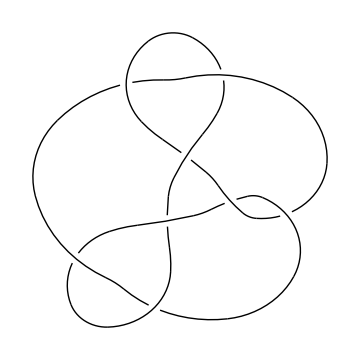

```mathematica
DrawPD[PD[Knot[8,15]],{Gap->0.03}]
```

```mathematica
knot=removePDCode[PD[Knot[8,15]]]
```

{{1,4,2,5},{3,8,4,9},{5,12,6,13},{13,16,14,1},{9,14,10,15},{15,10,16,11},{11,6,12,7},{7,2,8,3}}

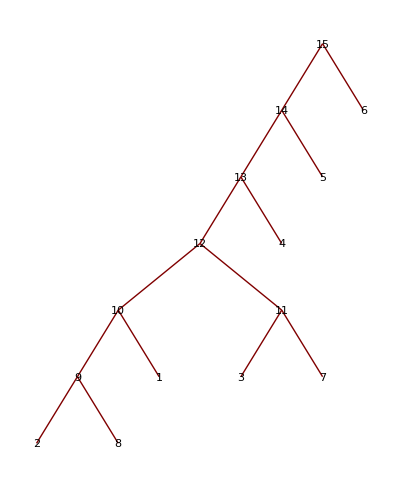
{{9→2,9→8,10→9,10→1,11→3,11→7,12→11,12→10,13→12,13→4,14→13,14→5,15→14,15→6},-Graphics-,{{{{3,8,4,9},{7,2,8,3}},{{4,9},{2,7}},9},{{{5,12,6,13},{11,6,12,7}},{{5,13},{7,11}},11},{{{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{7,9},{1,5}},10},{{1,4,2,5},{},1},{{3,8,4,9},{},2},{{5,12,6,13},{},3},{{7,2,8,3},{},8},{{9,14,10,15},{},5},{{11,6,12,7},{},7},{{13,16,14,1},{},4},{{15,10,16,11},{},6},{{{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{11,13},{1,9}},12},{{{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{9,11},{14,16}},13},{{{9,14,10,15},{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{11,16},{10,15}},14},{{{15,10,16,11},{9,14,10,15},{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{},{}},15}}}

```mathematica
findTangle[knot]
```

```mathematica
findTangle[knot]
```

{{9→2,9→8,10→9,10→1,11→3,11→7,12→11,12→10,13→12,13→4,14→13,14→5,15→14,15→6},-Graphics-}

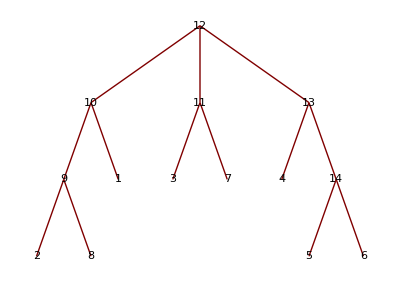

```mathematica
TreePlot[removeEliminate[findTangle[knot][[1]]],VertexLabeling->True]
```

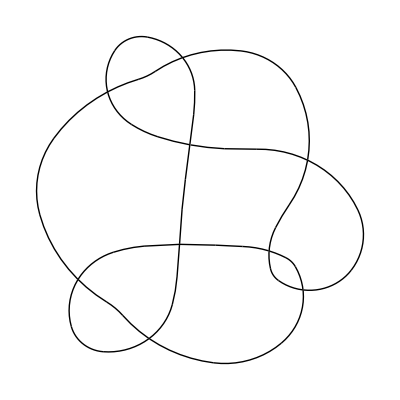

```mathematica
DrawPD[PD[Knot[9,28]]]
```

```mathematica
knot2=removePDCode[PD[Knot[9,28]]]
```

{{1,4,2,5},{3,8,4,9},{11,15,12,14},{5,13,6,12},{13,7,14,6},{15,18,16,1},{9,16,10,17},{17,10,18,11},{7,2,8,3}}

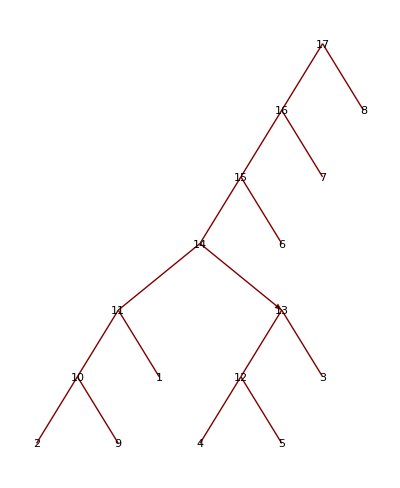
{{10→2,10→9,11→10,11→1,12→4,12→5,13→12,13→3,{14→13,eliminate},14→11,15→14,15→6,16→15,16→7,17→16,17→8},-Graphics-}

```mathematica
findTangle[knot2]
```

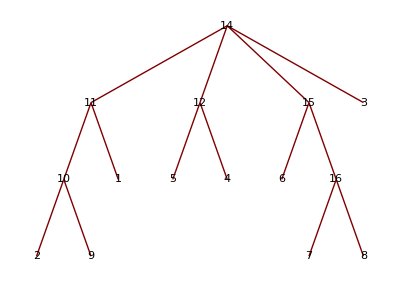

```mathematica
TreePlot[removeEliminate[{10->2,10->9,11->10,11->1,12->5,12->4,13->12,13->3,{14->13,"eliminate"},14->11,15->14,15->6,16->15,16->7,17->16,17->8}],VertexLabeling->True]
```

```mathematica
findTangle[knot2]
```

{{10→2,10→9,11→10,11→1,12→4,12→5,13→12,13→3,{14→13,eliminate},14→11,15→14,15→6,16→15,16→7,17→16,17→8},-Graphics-}

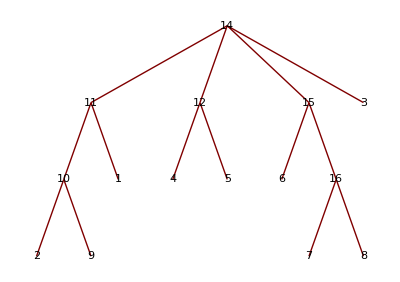

```mathematica
TreePlot[removeEliminate[findTangle[knot2][[1]]],VertexLabeling->True]
```

```mathematica
DrawPD[PD[Knot[8,16]]]
```

$Aborted

```mathematica
test333=PD[Knot[8,16]]
```

PD[X[6,2,7,1],X[14,6,15,5],X[16,11,1,12],X[12,7,13,8],X[8,3,9,4],X[4,9,5,10],X[10,15,11,16],X[2,14,3,13]]

```mathematica
knot3=removePDCode[PD[Knot[8,16]]]
```

{{6,2,7,1},{14,6,15,5},{16,11,1,12},{12,7,13,8},{8,3,9,4},{4,9,5,10},{10,15,11,16},{2,14,3,13}}

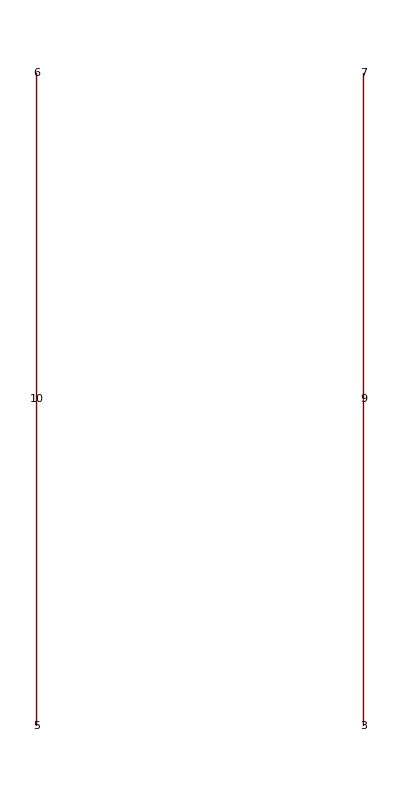
{{9→3,9→7,10→5,10→6},-Graphics-}

```mathematica
findTangle[knot3]
```

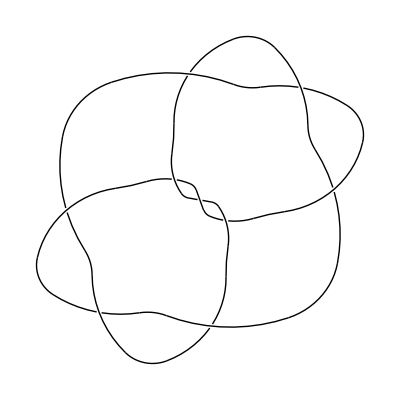

```mathematica
DrawPD[PD[Knot[9,35]]]
```

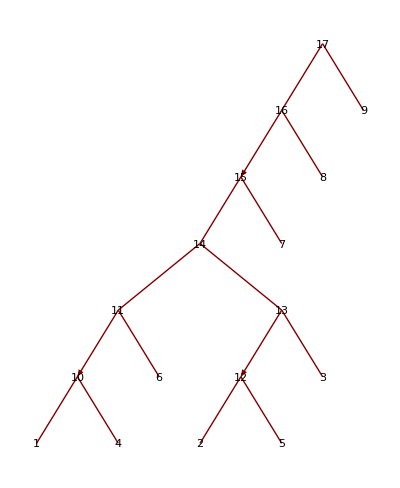
{{10→1,10→4,{11→10,eliminate},11→6,12→2,12→5,{13→12,eliminate},13→3,14→13,14→11,15→14,15→7,{16→15,eliminate},16→8,17→16,17→9},-Graphics-}

```mathematica
findTangle[removePDCode[PD[Knot[9,35]]]]
```

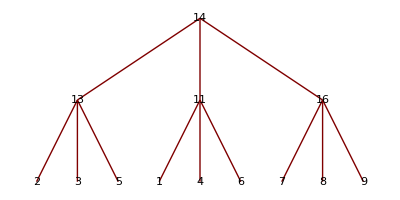

```mathematica
TreePlot[removeEliminate[{10->1,10->4,{11->10,"eliminate"},11->6,12->2,12->5,{13->12,"eliminate"},13->3,14->13,14->11,15->14,15->7,{16->15,"eliminate"},16->8,17->16,17->9}],VertexLabeling->True]
```

```mathematica
TreePlot[removeEliminate[findTangle[removePDCode[PD[Knot[9,35]]]][[1]]],VertexLabeling->True]
```

-Graphics-

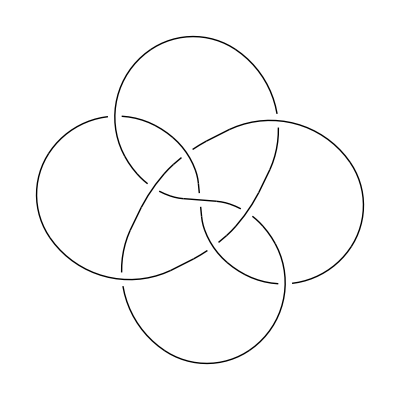

```mathematica
DrawPD[PD[Knot[9,40]],{Gap->0.03}]
```

```mathematica
findTangle[removePDCode[PD[Knot[9,40]]]]
```

No flyping circuits present

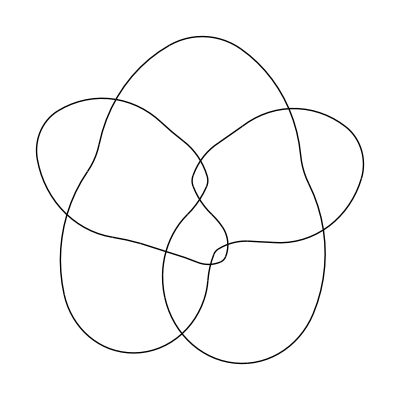

```mathematica
DrawPD[PD[Knot[10,158]]]
```

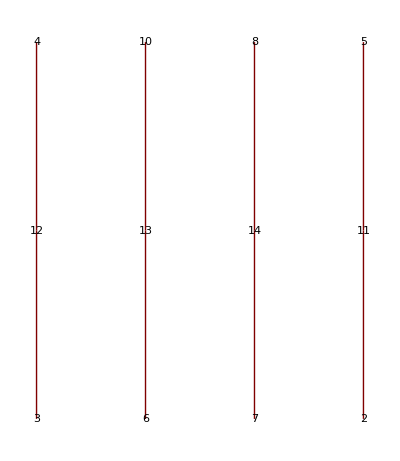
{{11→2,11→5,12→3,12→4,13→6,13→10,14→7,14→8},-Graphics-,{{{{3,10,4,11},{9,2,10,3}},{{4,11},{2,9}},11},{{{5,17,6,16},{17,5,18,4}},{{6,16},{4,18}},14},{{{8,14,9,13},{14,8,15,7}},{{7,15},{9,13}},12},{{{11,18,12,19},{19,12,20,13}},{{11,18},{13,20}},13},{{3,10,4,11},{},2},{{5,17,6,16},{},7},{{6,2,7,1},{},1},{{8,14,9,13},{},4},{{9,2,10,3},{},5},{{11,18,12,19},{},6},{{14,8,15,7},{},3},{{17,5,18,4},{},8},{{19,12,20,13},{},10},{{20,16,1,15},{},9}}}

```mathematica
findTangle[removePDCode[PD[Knot[10,158]]]]
```

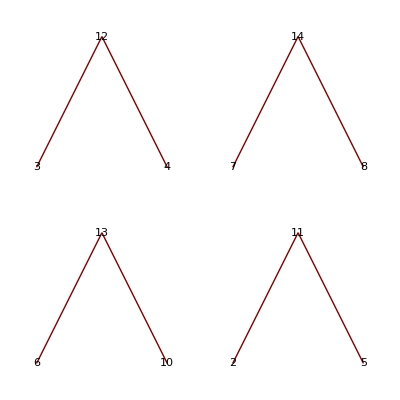

```mathematica
TreePlot[{11->2,11->5,12->3,12->4,13->6,13->10,14->7,14->8},Automatic,VertexLabeling->True]
```

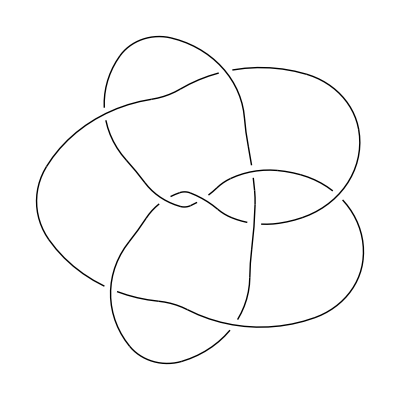

```mathematica
DrawPD[PD[Knot[9,41]],{Gap->0.03}]
```

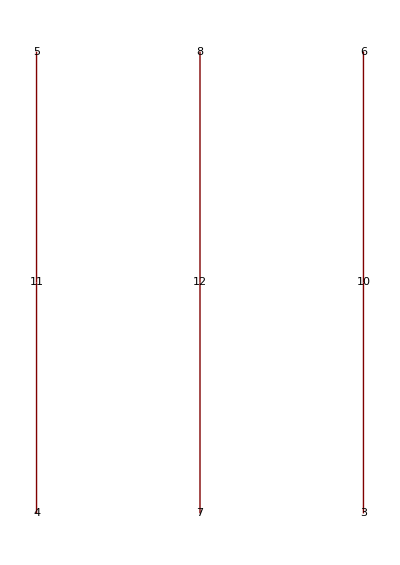
{{10→3,10→6,11→4,11→5,12→7,12→8},-Graphics-}

```mathematica
findTangle[removePDCode[PD[Knot[9,41]]]]
```

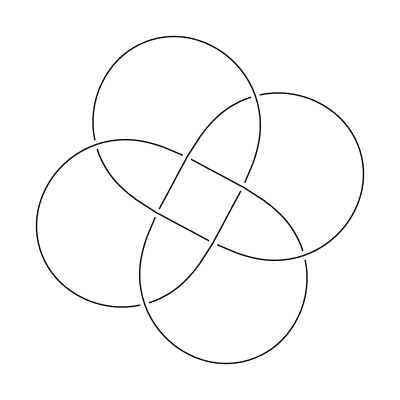

```mathematica
DrawPD[PD[Knot[8,18]]]
```

```mathematica
findTangle[removePDCode[PD[Knot[8,18]]]]
```

No flyping circuits present

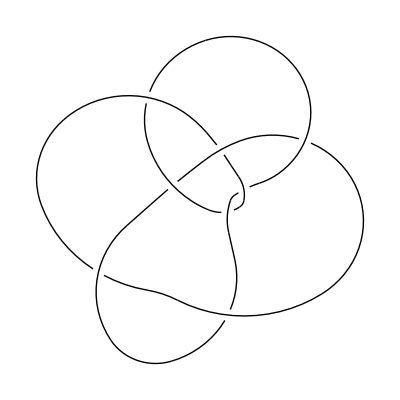

```mathematica
DrawPD[PD[Knot[8,17]]]
```

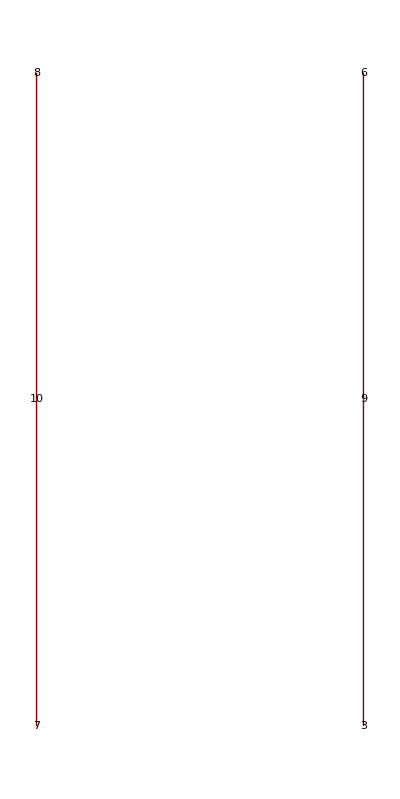
{{9→3,9→6,10→7,10→8},-Graphics-}

```mathematica
findTangle[removePDCode[PD[Knot[8,17]]]]
```

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

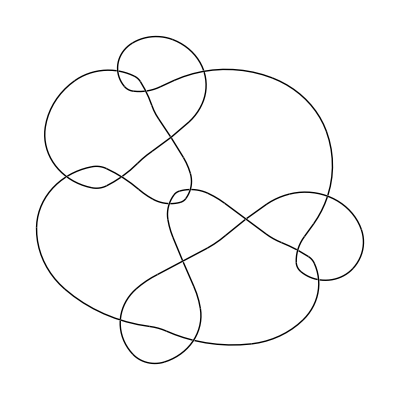

```mathematica
DrawPD[PD[Knot[15,Alternating,123]]]
```

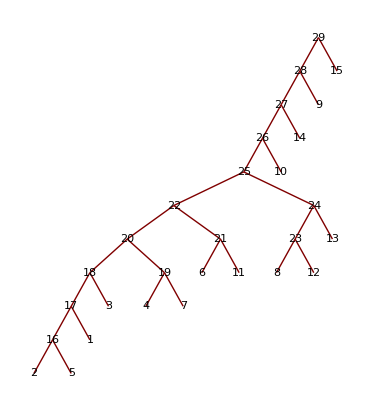
{{16→2,16→5,17→16,17→1,18→17,18→3,19→4,19→7,20→19,20→18,21→6,21→11,22→21,22→20,23→8,23→12,24→23,24→13,25→24,25→22,26→25,26→10,27→26,27→14,28→27,28→9,29→28,29→15},-Graphics-}

```mathematica
findTangle[removePDCode[PD[Knot[15,Alternating,123]]]]
```

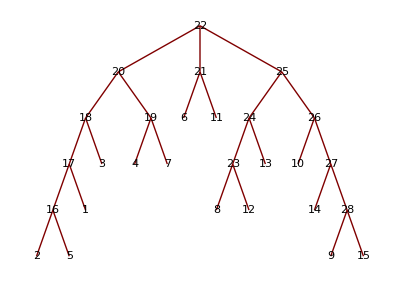

```mathematica
TreePlot[removeEliminate[findTangle[removePDCode[PD[Knot[15,Alternating,123]]]][[1]]],VertexLabeling->True]
```

```mathematica
Directory[]
```

C:\Users\trv63626\Documents

### Test Cases (for Test Order of PD Code)

```mathematica
testP1v1=removePDCode[PD[Knot[8,15]]]
```

{{1,4,2,5},{3,8,4,9},{5,12,6,13},{13,16,14,1},{9,14,10,15},{15,10,16,11},{11,6,12,7},{7,2,8,3}}

```mathematica
v1Perms=Permutations[testP1v1]
```

{{{1,4,2,5},{3,8,4,9},{5,12,6,13},{13,16,14,1},{9,14,10,15},{15,10,16,11},{11,6,12,7},{7,2,8,3}},{{1,4,2,5},{3,8,4,9},{5,12,6,13},{13,16,14,1},{9,14,10,15},{15,10,16,11},{7,2,8,3},{11,6,12,7}},{{1,4,2,5},{3,8,4,9},{5,12,6,13},{13,16,14,1},{9,14,10,15},{11,6,12,7},{15,10,16,11},{7,2,8,3}},40314,{{7,2,8,3},{11,6,12,7},{15,10,16,11},{9,14,10,15},{13,16,14,1},{3,8,4,9},{5,12,6,13},{1,4,2,5}},{{7,2,8,3},{11,6,12,7},{15,10,16,11},{9,14,10,15},{13,16,14,1},{5,12,6,13},{1,4,2,5},{3,8,4,9}},{{7,2,8,3},{11,6,12,7},{15,10,16,11},{9,14,10,15},{13,16,14,1},{5,12,6,13},{3,8,4,9},{1,4,2,5}}}
 |  |  |  |

```mathematica
testP1v2=v1Perms[[12000]]
```

{{5,12,6,13},{13,16,14,1},{15,10,16,11},{7,2,8,3},{11,6,12,7},{9,14,10,15},{3,8,4,9},{1,4,2,5}}

```mathematica
testP1v3=v1Perms[[32000]]
```

{{11,6,12,7},{5,12,6,13},{13,16,14,1},{15,10,16,11},{3,8,4,9},{1,4,2,5},{7,2,8,3},{9,14,10,15}}

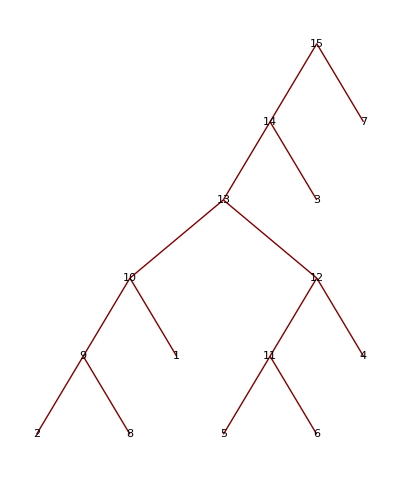
{{9→2,9→8,10→9,10→1,11→5,11→6,12→11,12→4,13→12,13→10,14→13,14→3,15→14,15→7},-Graphics-}

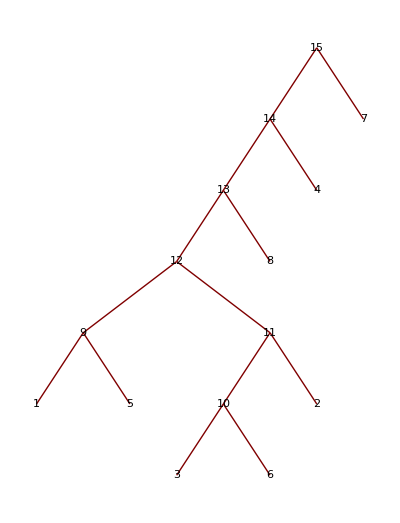
{{9→1,9→5,10→3,10→6,11→10,11→2,12→11,12→9,13→12,13→8,14→13,14→4,15→14,15→7},-Graphics-}

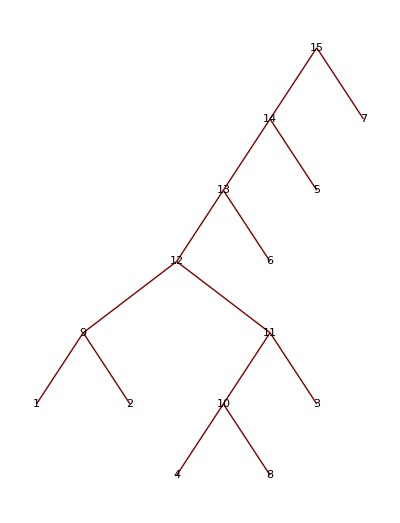
{{9→1,9→2,10→4,10→8,11→10,11→3,12→11,12→9,13→12,13→6,14→13,14→5,15→14,15→7},-Graphics-}

```mathematica
findTangle[testP1v1]
findTangle[testP1v2]
findTangle[testP1v3]
```

```mathematica
testP2v1=removePDCode[PD[Knot[8,6]]]
```

{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}

```mathematica
v2Perms=Permutations[testP2v1]
```

{{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}},{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{13,8,14,9},{15,6,16,7}},{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{15,6,16,7},{7,16,8,1},{13,8,14,9}},40314,{{13,8,14,9},{15,6,16,7},{7,16,8,1},{5,14,6,15},{11,3,12,2},{9,12,10,13},{3,11,4,10},{1,4,2,5}},{{13,8,14,9},{15,6,16,7},{7,16,8,1},{5,14,6,15},{11,3,12,2},{3,11,4,10},{1,4,2,5},{9,12,10,13}},{{13,8,14,9},{15,6,16,7},{7,16,8,1},{5,14,6,15},{11,3,12,2},{3,11,4,10},{9,12,10,13},{1,4,2,5}}}
 |  |  |  |

```mathematica
testP2v2=v2Perms[[20000]]
```

{{11,3,12,2},{13,8,14,9},{7,16,8,1},{5,14,6,15},{9,12,10,13},{1,4,2,5},{15,6,16,7},{3,11,4,10}}

```mathematica
testP2v3=v2Perms[[36000]]
```

{{13,8,14,9},{1,4,2,5},{15,6,16,7},{7,16,8,1},{5,14,6,15},{11,3,12,2},{3,11,4,10},{9,12,10,13}}

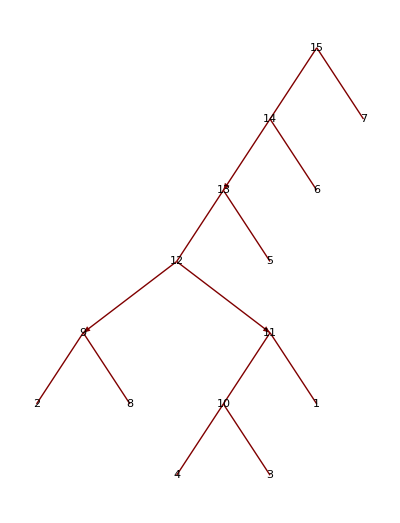
{{9→2,9→8,10→4,10→3,11→10,11→1,{12→11,eliminate},{12→9,eliminate},13→12,13→5,{14→13,eliminate},14→6,15→14,15→7},-Graphics-}

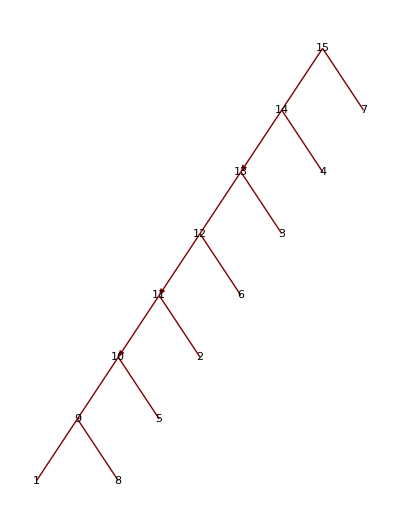
{{9→1,9→8,10→9,10→5,{11→10,eliminate},11→2,{12→11,eliminate},12→6,13→12,13→3,{14→13,eliminate},14→4,15→14,15→7},-Graphics-}

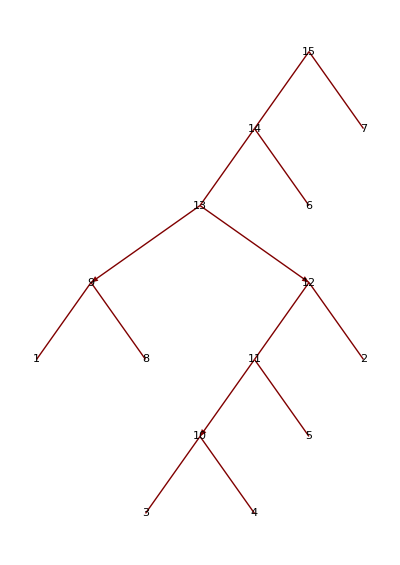
{{9→1,9→8,10→3,10→4,{11→10,eliminate},11→5,12→11,12→2,{13→12,eliminate},{13→9,eliminate},14→13,14→6,15→14,15→7},-Graphics-}

```mathematica
findTangle[testP2v1]
findTangle[testP2v2]
findTangle[testP2v3]
```

### Test Order of PD Code

#### Check Unique Trees

```mathematica
checkUniqueTrees[edgesPermutations_]:=Module[{listSet,treeSet,pdSet,i,tempData,tempTree},
listSet={};
treeSet={};
pdSet={};
(*for each permutation of the PD-code...*)
For[i=1,i≤Length[edgesPermutations],i++,
(*Get the non-reduced edges and tree for that PD-code*)
tempData=findTangle[edgesPermutations[[i]]];
(*Convert the edges of the tree to a list-representation of that structure*)
tempTree=graphToList[tempData[[1]]];
(*If this permutation's tree structure is not already contained in the 'listSet'...*)
If[!MemberQ[listSet,tempTree],
(*then append that list-representaton to 'listSet.'*)
AppendTo[listSet,tempTree];
(*append the tree itself to 'treeSet.'*)
AppendTo[treeSet,tempData[[2]]];
(*append the PD-code to 'pdSet.'*)
AppendTo[pdSet,edgesPermutations[[i]]];
Print[tempTree];
];
];
(*return the list of the PD-codes and distinct non-reduced trees*)
Return[{pdSet,treeSet}];
]
```

```mathematica
checkUniqueTrees[v1Perms]
```

{{1,4,2,5},{3,8,4,9},{5,12,6,13},{13,16,14,1},{9,14,10,15},{15,10,16,11},{11,6,12,7},{7,2,8,3}}

{{1,4,2,5},{3,8,4,9},{5,12,6,13},{13,16,14,1},{11,6,12,7},{9,14,10,15},{15,10,16,11},{7,2,8,3}}

{{1,4,2,5},{5,12,6,13},{3,8,4,9},{13,16,14,1},{9,14,10,15},{15,10,16,11},{11,6,12,7},{7,2,8,3}}

$Aborted

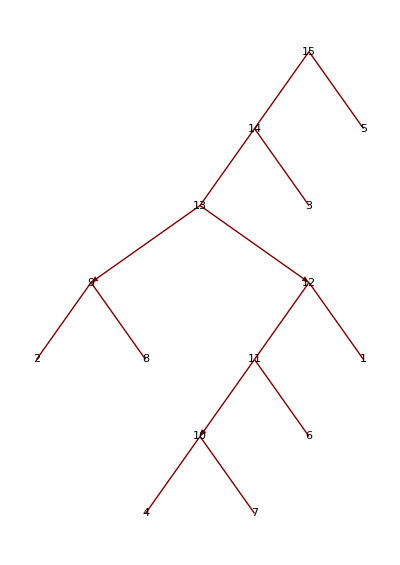
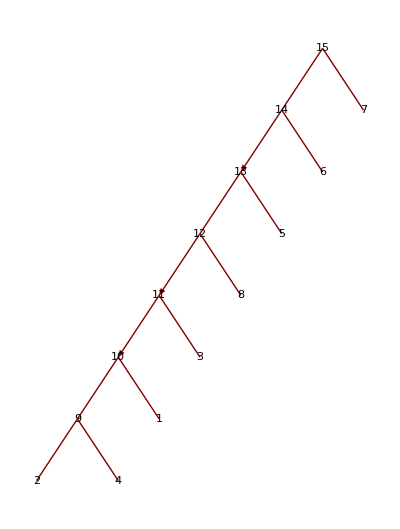
```mathematica
{{{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}},{{1,4,2,5},{9,12,10,13},{3,11,4,10},{5,14,6,15},{11,3,12,2},{7,16,8,1},{15,6,16,7},{13,8,14,9}},{{1,4,2,5},{3,11,4,10},{9,12,10,13},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}},{-Graphics-,-Graphics-,-Graphics-}}[[1]]
```

{{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}},{{1,4,2,5},{9,12,10,13},{3,11,4,10},{5,14,6,15},{11,3,12,2},{7,16,8,1},{15,6,16,7},{13,8,14,9}},{{1,4,2,5},{3,11,4,10},{9,12,10,13},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}}

```mathematica
checkUniqueTrees[v2Perms]
```

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{{{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}},{{1,4,2,5},{9,12,10,13},{3,11,4,10},{5,14,6,15},{11,3,12,2},{7,16,8,1},{15,6,16,7},{13,8,14,9}},{{1,4,2,5},{3,11,4,10},{9,12,10,13},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}},{-Graphics-,-Graphics-,-Graphics-}}

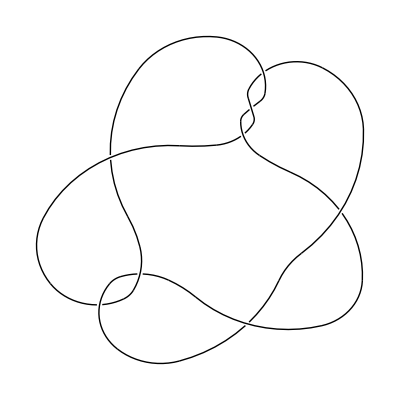

```mathematica
DrawPD[PD[Knot[8,6]]]
```

```mathematica
DrawPD[replacePDCode[{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}]]
```

-Graphics-

```mathematica
DrawPD[replacePDCode[{{1,4,2,5},{9,12,10,13},{3,11,4,10},{5,14,6,15},{11,3,12,2},{7,16,8,1},{15,6,16,7},{13,8,14,9}}]]
```

-Graphics-

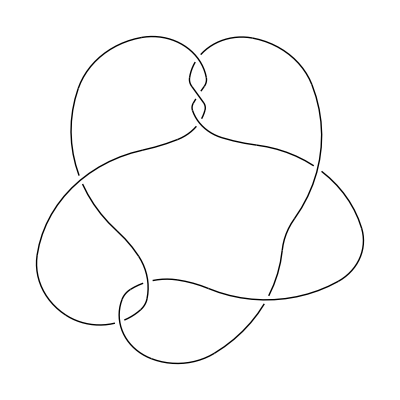

```mathematica
DrawPD[replacePDCode[{{1,4,2,5},{3,11,4,10},{9,12,10,13},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}]]
```

```mathematica
Replace[{15,{14,{13,{12,{11,{5,{},{}},{6,{},{}}},{4,{},{}}},{10,{9,{2,{},{}},{8,{},{}}},{1,{},{}}}},{3,{},{}}},{7,{},{}}},NumberQ[x]->x]
```

{15,{14,{13,{12,{11,{5,{},{}},{6,{},{}}},{4,{},{}}},{10,{9,{2,{},{}},{8,{},{}}},{1,{},{}}}},{3,{},{}}},{7,{},{}}}

```mathematica
graphToList[findTangle[testP1v1][[1]]]
graphToList[findTangle[testP1v2][[1]]]
graphToList[findTangle[testP1v3][[1]]]
```

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

```mathematica
graphToList[findTangle[testP1v1][[1]]]==graphToList[findTangle[testP1v2][[1]]]
```

False

```mathematica
graphToList[findTangle[testP1v2][[1]]]==graphToList[findTangle[testP1v3][[1]]]
```

True

```mathematica
graphToList[{9->2,9->8,10->9,10->1,11->5,11->6,12->11,12->4,{13->12,"eliminate"},{13->10,"eliminate"},{14->13,"eliminate"},14->3,{15->14,"eliminate"},15->7}]
```

{15,{14,{13,{12,{11,{5,{},{}},{6,{},{}}},{4,{},{}}},{10,{9,{2,{},{}},{8,{},{}}},{1,{},{}}}},{3,{},{}}},{7,{},{}}}

```mathematica
graphToList[{9->1,9->2,10->4,10->8,11->10,11->3,{12->11,"eliminate"},{12->9,"eliminate"},{13->12,"eliminate"},13->6,{14->13,"eliminate"},14->5,{15->14,"eliminate"},15->7}]
```

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

```mathematica
makeChildMap[{9->2,9->8,10->9,10->1,11->5,11->6,12->11,12->4,13->12,13->10,14->13,14->3,15->14,15->7}]
```

<|9→{2,8},10→{9,1},11→{5,6},12→{11,4},13→{12,10},14→{13,3},15→{14,7}|>

```mathematica
sameOrderEdges[{9->2,9->8,10->9,10->1,11->5,11->6,12->11,12->4,{13->12,"eliminate"},{13->10,"eliminate"},{14->13,"eliminate"},14->3,{15->14,"eliminate"},15->7}]
```

{9→2,9→8,10→9,10→1,11→5,11→6,12→11,12→4,13→12,13→10,14→13,14→3,15→14,15→7}

```mathematica
convertEdgesToList[{9->2,9->8,10->9,10->1,11->5,11->6,12->11,12->4,{13->12,"eliminate"},{13->10,"eliminate"},{14->13,"eliminate"},14->3,{15->14,"eliminate"},15->7}]
```

{{2,9},{8,9},{9,10},{1,10},{5,11},{6,11},{11,12},{4,12},{12,13},{10,13},{13,14},{3,14},{14,15},{7,15}}

```mathematica
Association[reverseEdges[{9->2,9->8,10->9,10->1,11->5,11->6,12->11,12->4,{13->12,"eliminate"},{13->10,"eliminate"},{14->13,"eliminate"},14->3,{15->14,"eliminate"},15->7}]]
```

<|2→9,8→9,9→10,1→10,5→11,6→11,11→12,4→12,12→13,10→13,13→14,3→14,14→15,7→15|>

```mathematica
Length[{9->2,9->8,10->9,10->1,11->5,11->6,12->11,12->4,{13->12,"eliminate"},{13->10,"eliminate"},{14->13,"eliminate"},14->3,{15->14,"eliminate"},15->7}]
```

14

### Helper Functions

```mathematica
(*function is given a list of edges and returns a list-representation of the tree structure of those edges.*)
graphToList[edgesLst_]:=Module[{childToParent,parentToChild,maxIndex,i,edgesVersion},
(*convert the list of edges to a list of edges without any 'eliminates'. The edges marked for eliminate will remain, though the 'eliminate' labels will not.*)
parentToChild=sameOrderEdges[edgesLst];
(*convert the list of edges (without 'eliminate' labels) to a map/association of each parent to a list of its children.*)
parentToChild=makeChildMap[parentToChild];
(*The greatest index value equals one plus the length of the list of edges*)
maxIndex=Length[edgesLst]+1;

(*Return the recursive result that is a list of a vertex followed by its children.*)
Return[getChildren[maxIndex,parentToChild]];
]
```

```mathematica
getChildren[index_,parentToChild_]:=Module[{child1,child2,parentToChildren=parentToChild,count=1,i},
(*If the given index does not have any chidren (if it is a leaf)...*)
If[!MemberQ[Keys[parentToChild],index],
(*then return an x-symbol followed by two sets of empty curly-braces*)
Return[{x,{},{}}];
];
(*child 1 is the first child in the list of children for the given parent index (in the parentToChild map/association).*)
child1=parentToChild[index][[1]];
(*child 2 is the second child in the list of children for the given parent index (in the parentToChild map/association).*)
child2=parentToChild[index][[2]];
(*return an x-symbol followed by the output of getChildren with child1 as the input, and the output of getChildren with child2 as the input.*)
Return[{x,getChildren[child1,parentToChild],getChildren[child2,parentToChild]}];
]
```

```mathematica
makeChildMap[parentToChildren_]:=Module[{map,i,j},
(*initialize a new association/map*)
map=Association[];
(*make each parent in the tree a key in the association/map.*)
For[i=1,i≤Length[parentToChildren],i++,
AppendTo[map,parentToChildren[[i,1]]->{}];
];

(*for each edge, append the child to the list that is mapped to its parent index.*)
For[j=1,j≤Length[parentToChildren],j++,
AppendTo[map[parentToChildren[[j,1]]],parentToChildren[[j,2]]];
];

(*return the map/association of the parent indices to the lists of their children.*)
Return[map];
]
```

```mathematica
convertEdgesToList[edges_]:=Module[{newList},
newList=Table[
If[edges[[i,2]]=="eliminate",
{edges[[i,1,2]],edges[[i,1,1]]},
{edges[[i,2]],edges[[i,1]]}
]
,{i,1,Length[edges]}
];
Return[newList];
]
```

```mathematica
(*returns a list of edges without the 'eliminate' labels. The edges marked by 'eliminate' remain in the list without the labels.*)
sameOrderEdges[edges_]:=Module[{newList},
newList=Table[
If[edges[[i,2]]=="eliminate",
edges[[i,1,1]]->edges[[i,1,2]],
edges[[i,1]]->edges[[i,2]]
]
,{i,1,Length[edges]}
];
Return[newList];
]
```

```mathematica
(*returns a reversed list of edges without the 'eliminate' labels. The edges marked by 'eliminate' remain in the list without the labels.
	The output is the same as that of the sameOrderEdges function, but the edges are in reversed order. This creates a list of edges
		from each child to its parent.*)
reverseEdges[edges_]:=Module[{newList},
newList=Table[
If[edges[[i,2]]=="eliminate",
edges[[i,1,2]]->edges[[i,1,1]],
edges[[i,2]]->edges[[i,1]]
]
,{i,1,Length[edges]}
];
Return[newList];
]
```

```mathematica
(*converts an assocation of parent indices to lists of children into a list of edges from the parent indices to each of their children.*)
convertMapToList[map_]:=Module[{newList={},list,i,j,parent,children},
list=Normal[map];
For[i=1,i≤Length[list],i++,
parent=list[[i,1]];
children=map[parent];
For[j=1,j≤Length[children],j++,
AppendTo[newList,parent->children[[j]]];
]
];
Return[newList];
]
```

### Remove ‘eliminate’

```mathematica
(*given a list of edges, removeEliminate returns a list of the edges after the edges marked for elimination have been removed and the tree has been adjusted.*)
removeEliminate[edgesList_]:=Module[{newEdges={},edges=edgesList,i,j,k,parent,child,childrenMap,newChildren,oldParents={},oldChildren,edgesSimp,elims},
(*create a map from each parent to a list of their children.*)
childrenMap=makeChildMap[sameOrderEdges[edgesList]];
(*Print@childrenMap;*)
(*select the edges that are marked for elimination and store them in 'elims.'*)
elims=Select[edgesList,#[[2]]=="eliminate"&];
(*Print@elims;*)
(*For each edge marked for elimination...*)
Table[
(*the parent is the first element in the edge.*)
parent=elimElement[[1,1]];
(*the child is the second element in the edge.*)
child=elimElement[[1,2]];

(*get new children*)
newChildren=childrenMap[child];

(*make each of the new children be children of the new parent*)
oldChildren=childrenMap[parent];
oldChildren=oldChildren/.child->Nothing;

AppendTo[childrenMap,parent->Union[oldChildren,newChildren]];
childrenMap=KeyDrop[childrenMap,child];
,{elimElement,elims}];

(*'adjust' the first edge by pruning the edge that leads from the max index to a non-leaf tangle.*)
childrenMap=adjustFirstEdge[childrenMap];

(*convert the map of the parents to their children into a list of edges.*)
newEdges=convertMapToList[childrenMap];

(*return the list 'newEdges' which contains a list of the edges after the 'eliminate' edges have been removed and the tree has been adjusted.*)
Return[newEdges];
]
```

```mathematica
(*'adjust' the first edge by pruning the edge that leads from the max index to a non-leaf tangle.*)
adjustFirstEdge[map_]:=Module[{newMap=map,keys,lastIndex,transferValue},
keys=Sort[Keys[map]];
lastIndex=Last[keys];
transferValue=Select[map[lastIndex],#≠lastIndex-1&];
AppendTo[newMap,lastIndex-1->Union[map[lastIndex-1],transferValue]];
newMap=KeyDrop[newMap,lastIndex];

Return[newMap];
]
```

#### Three different non-reduced trees (corresponding to the same knot diagram) yield the same reduced tree

Part::partd: Part specification testP2v1⟦1⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Union::heads: Heads List and Missing at positions 2 and 1 are expected to be the same.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Union::heads: Heads List and Missing at positions 2 and 1 are expected to be the same.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Union::heads: Heads List and Missing at positions 2 and 1 are expected to be the same.

General::stop: Further output of Union::heads will be suppressed during this calculation.

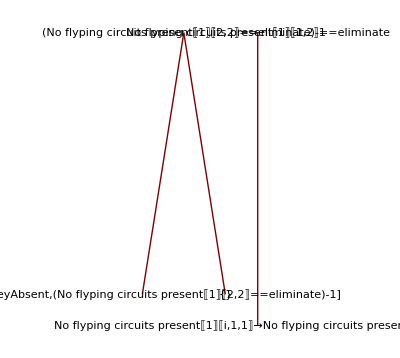
No flyping circuits present⟦2⟧No flyping circuits present⟦2⟧No flyping circuits present⟦2⟧
-Graphics--Graphics--Graphics-

```mathematica
Column[{Row[{findTangle[testP2v1][[2]],
findTangle[testP2v2][[2]],
findTangle[testP2v3][[2]]}],
Row[{TreePlot[removeEliminate[findTangle[testP2v1][[1]]],VertexLabeling->True],
TreePlot[removeEliminate[findTangle[testP2v2][[1]]],VertexLabeling->True],
TreePlot[removeEliminate[findTangle[testP2v3][[1]]],VertexLabeling->True]}]
}]
```

```mathematica
test10=removePDCode[PD[Knot[10,67]]]
```

KnotTheory::loading: Loading precomputed data in PD4Knots`.

{{1,4,2,5},{7,12,8,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{9,18,10,19},{15,20,16,1},{19,16,20,17},{17,8,18,9}}

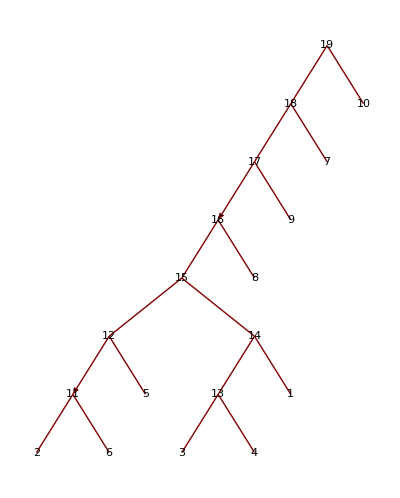
{{11→2,11→6,{12→11,eliminate},12→5,13→3,13→4,14→13,14→1,15→14,15→12,16→15,16→8,{17→16,eliminate},17→9,18→17,18→7,19→18,19→10},-Graphics-,{{{{3,11,4,10},{11,3,12,2}},{{4,10},{2,12}},13},{{{7,12,8,13},{13,6,14,7}},{{8,12},{6,14}},11},{{{3,11,4,10},{11,3,12,2},{1,4,2,5}},{{10,12},{1,5}},14},{{{7,12,8,13},{13,6,14,7},{5,14,6,15}},{{8,12},{5,15}},12},{{1,4,2,5},{},1},{{3,11,4,10},{},3},{{5,14,6,15},{},5},{{7,12,8,13},{},2},{{9,18,10,19},{},7},{{11,3,12,2},{},4},{{13,6,14,7},{},6},{{15,20,16,1},{},8},{{17,8,18,9},{},10},{{19,16,20,17},{},9},{{{3,11,4,10},{11,3,12,2},{1,4,2,5},{7,12,8,13},{13,6,14,7},{5,14,6,15}},{{1,10},{8,15}},15},{{{15,20,16,1},{3,11,4,10},{11,3,12,2},{1,4,2,5},{7,12,8,13},{13,6,14,7},{5,14,6,15}},{{8,10},{16,20}},16},{{{19,16,20,17},{15,20,16,1},{3,11,4,10},{11,3,12,2},{1,4,2,5},{7,12,8,13},{13,6,14,7},{5,14,6,15}},{{8,10},{17,19}},17},{{{9,18,10,19},{19,16,20,17},{15,20,16,1},{3,11,4,10},{11,3,12,2},{1,4,2,5},{7,12,8,13},{13,6,14,7},{5,14,6,15}},{{8,17},{9,18}},18},{{{17,8,18,9},{9,18,10,19},{19,16,20,17},{15,20,16,1},{3,11,4,10},{11,3,12,2},{1,4,2,5},{7,12,8,13},{13,6,14,7},{5,14,6,15}},{{},{}},19}}}

```mathematica
test1234=findTangle[{{1,4,2,5},{7,12,8,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{9,18,10,19},{15,20,16,1},{19,16,20,17},{17,8,18,9}}]
```

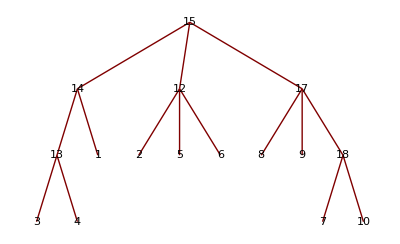

```mathematica
TreePlot[removeEliminate[findTangle[{{1,4,2,5},{7,12,8,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{9,18,10,19},{15,20,16,1},{19,16,20,17},{17,8,18,9}}][[1]]
],VertexLabeling->True]
```

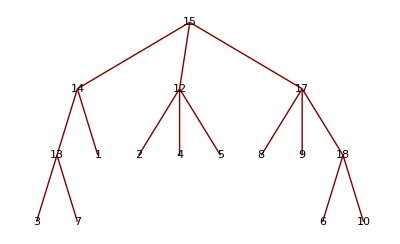

```mathematica
TreePlot[removeEliminate[findTangle[{{1,4,2,5},{7,12,8,13},{3,11,4,10},{5,14,6,15},{13,6,14,7},{9,18,10,19},{11,3,12,2},{15,20,16,1},{19,16,20,17},{17,8,18,9}}][[1]]],VertexLabeling->True]
```

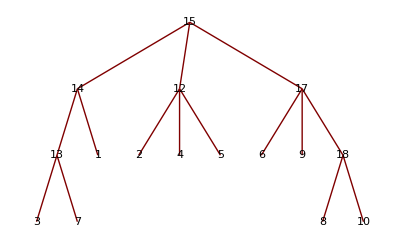

TreePlot[removeEliminate[findTangle[{{1,4,2,5},{7,12,8,13},{3,11,4,10},{5,14,6,15},{13,6,14,7},{15,20,16,1},{9,18,10,19},{11,3,12,2},{19,16,20,17},{17,8,18,9}}][[1]]]]

```mathematica
TreePlot[removeEliminate[findTangle[{{1,4,2,5},{7,12,8,13},{3,11,4,10},{5,14,6,15},{13,6,14,7},{15,20,16,1},{11,3,12,2},{9,18,10,19},{19,16,20,17},{17,8,18,9}}][[1]]],VertexLabeling->True]
```

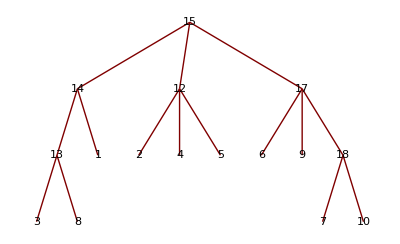

```mathematica
TreePlot[removeEliminate[findTangle[{{1,4,2,5},{7,12,8,13},{3,11,4,10},{5,14,6,15},{13,6,14,7},{15,20,16,1},{9,18,10,19},{11,3,12,2},{19,16,20,17},{17,8,18,9}}][[1]]],VertexLabeling->True]
```

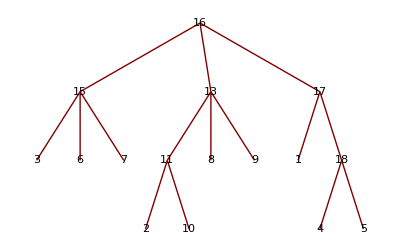

```mathematica
TreePlot[removeEliminate[findTangle[{{1,4,2,5},{9,18,10,19},{7,12,8,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{15,20,16,1},{19,16,20,17},{17,8,18,9}}][[1]]],VertexLabeling->True]
```

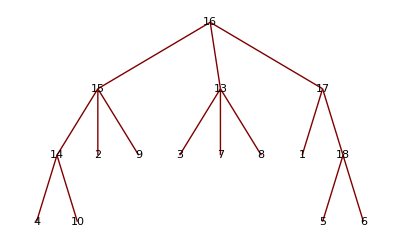

```mathematica
TreePlot[removeEliminate[findTangle[{{1,4,2,5},{15,20,16,1},{7,12,8,13},{9,18,10,19},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{19,16,20,17},{17,8,18,9}}][[1]]],VertexLabeling->True]
```

#### Testing

```mathematica
test1=findTangle[testP2v1]
```

Part::partd: Part specification testP2v1⟦1⟧ is longer than depth of object.

No flyping circuits present

```mathematica
tree1=removeEliminate[test1[[1]]]
```

Part::partd: Part specification No flyping circuits present⟦1⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦1⟧⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦1⟧⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Union::heads: Heads List and Missing at positions 2 and 1 are expected to be the same.

{No flyping circuits present⟦1⟧⟦1,2⟧==eliminate→No flyping circuits present⟦1⟧⟦i,1,1⟧→No flyping circuits present⟦1⟧⟦i,1,2⟧,-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)→Missing[KeyAbsent,-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)],-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)→{}}

```mathematica
TreePlot[tree1,VertexLabeling->True]
```

-Graphics-

```mathematica
test2=findTangle[testP2v2]
```

Part::partd: Part specification testP2v2⟦1⟧ is longer than depth of object.

No flyping circuits present

```mathematica
tree2=removeEliminate[test2[[1]]]
```

Part::partd: Part specification No flyping circuits present⟦1⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦1⟧⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦1⟧⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Union::heads: Heads List and Missing at positions 2 and 1 are expected to be the same.

{No flyping circuits present⟦1⟧⟦1,2⟧==eliminate→No flyping circuits present⟦1⟧⟦i,1,1⟧→No flyping circuits present⟦1⟧⟦i,1,2⟧,-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)→Missing[KeyAbsent,-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)],-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)→{}}

```mathematica
TreePlot[tree2,VertexLabeling->True]
```

-Graphics-

```mathematica
test3=findTangle[testP2v3]
```

Part::partd: Part specification testP2v3⟦1⟧ is longer than depth of object.

No flyping circuits present

```mathematica
tree3=removeEliminate[test3[[1]]]
```

Part::partd: Part specification No flyping circuits present⟦1⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦1⟧⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦1⟧⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Union::heads: Heads List and Missing at positions 2 and 1 are expected to be the same.

{No flyping circuits present⟦1⟧⟦1,2⟧==eliminate→No flyping circuits present⟦1⟧⟦i,1,1⟧→No flyping circuits present⟦1⟧⟦i,1,2⟧,-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)→Missing[KeyAbsent,-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)],-1+(No flyping circuits present⟦1⟧⟦2,2⟧==eliminate)→{}}

```mathematica
TreePlot[tree3,VertexLabeling->True]
```

-Graphics-

```mathematica
findTangle[testP1v1][[2]]
findTangle[testP1v2][[2]]
findTangle[testP1v3][[2]]
```

Part::partd: Part specification testP1v1⟦1⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦2⟧ is longer than depth of object.

No flyping circuits present⟦2⟧

Part::partd: Part specification testP1v2⟦1⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦2⟧ is longer than depth of object.

No flyping circuits present⟦2⟧

Part::partd: Part specification testP1v3⟦1⟧ is longer than depth of object.

Part::partd: Part specification No flyping circuits present⟦2⟧ is longer than depth of object.

No flyping circuits present⟦2⟧

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

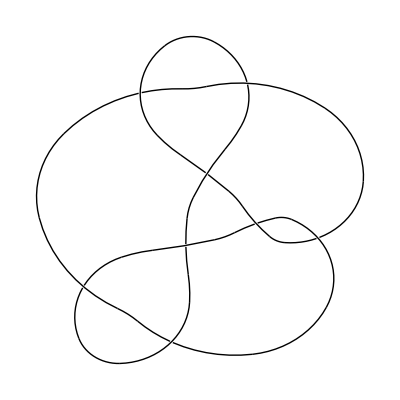

```mathematica
DrawPD[PD[Knot[8,15]]]
```

### Combined Function - displays non-reduced and reduced trees given a knot’s PD-code

```mathematica
overallTrees[pd_]:=Module[{listPerms,distinctPDlist,distinctTrees,distinctReducedTrees,nonReducedTrees,reducedTrees},
(*peremute the given PD-code*)
listPerms=Permutations[pd];
(*get the list of the pd-codes for the distinct trees betweent the PD-code permutations.*)
distinctPDlist=checkUniqueTrees[listPerms][[1]];

(*create a table of the distinct non-reduced trees. This is obtained from running findTangle with the PD-code of each distinct tree as the input.*)
distinctTrees=Table[findTangle[distinctPDlist[[i]]][[1]],{i,1,Length[distinctPDlist]}];
(*create a table of the reduced versions of the distinct non-reduced trees. This is obtained by running removeEliminate with the edges of the distinct non-reduced trees as the input.*)
distinctReducedTrees=Table[removeEliminate[distinctTrees[[i]]],{i,1,Length[distinctTrees]}];

(*create TreePlots using the edges of the distinct non-reduced trees.*)
nonReducedTrees=Table[TreePlot[distinctTrees[[i]],VertexLabeling->True],{i,1,Length[distinctTrees]}];
(*create TreePlots using the edges of the reduced trees.*)
reducedTrees=Table[TreePlot[distinctReducedTrees[[i]],VertexLabeling->True],{i,1,Length[distinctReducedTrees]}];

(*return the lists of distinct PD-codes, non-reduced trees, and reduced trees.*)
Return[{distinctPDlist,nonReducedTrees,reducedTrees}]
]
```

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

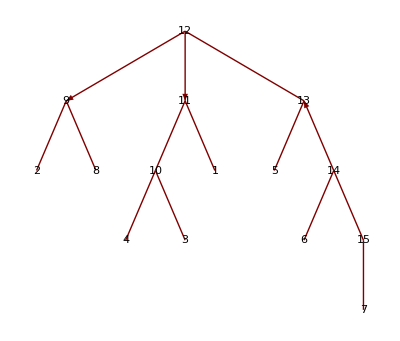
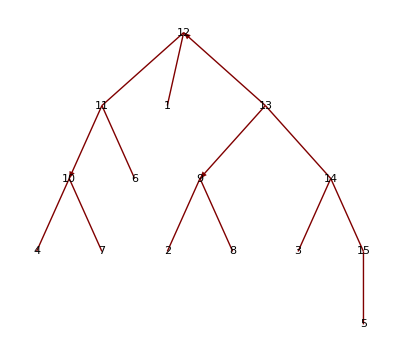
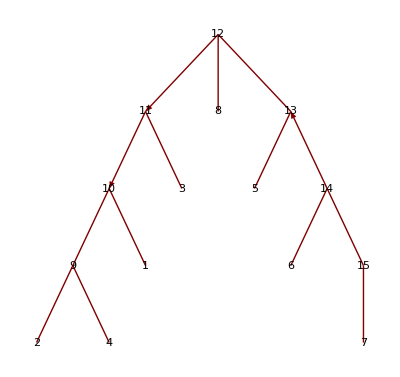
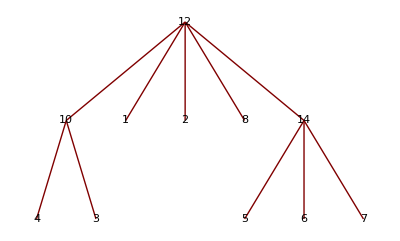
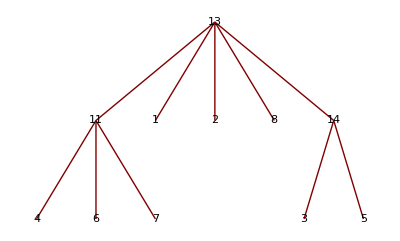
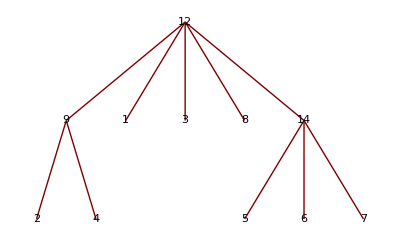
{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}} | {{1,4,2,5},{9,12,10,13},{3,11,4,10},{5,14,6,15},{11,3,12,2},{7,16,8,1},{15,6,16,7},{13,8,14,9}} | {{1,4,2,5},{3,11,4,10},{9,12,10,13},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[8,6]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

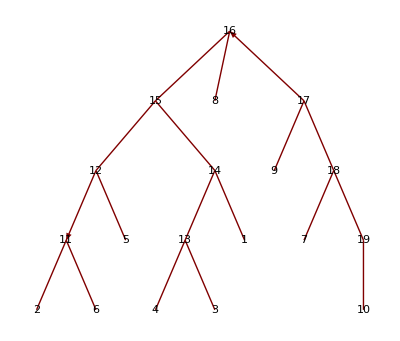
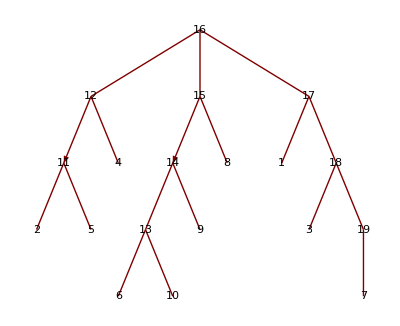
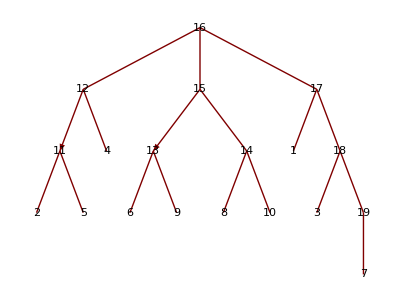
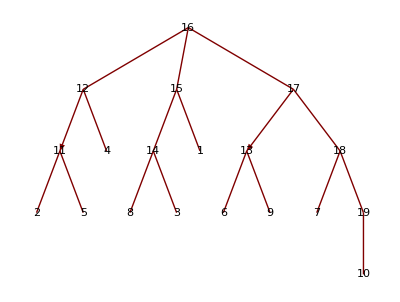
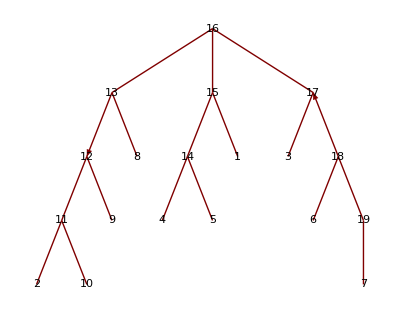
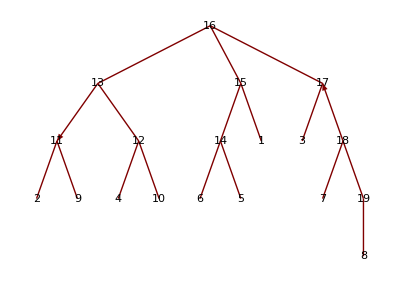
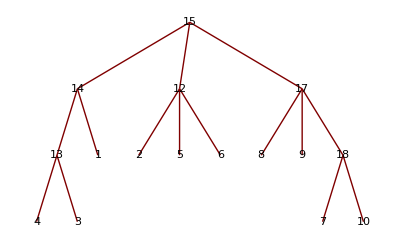
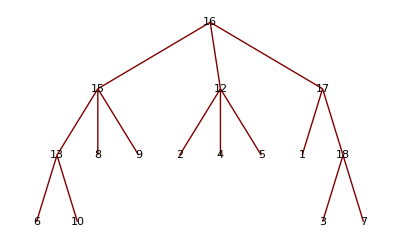
{{1,4,2,5},{7,12,8,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{9,18,10,19},{15,20,16,1},{19,16,20,17},{17,8,18,9}} | {{1,4,2,5},{7,12,8,13},{3,11,4,10},{5,14,6,15},{13,6,14,7},{9,18,10,19},{11,3,12,2},{15,20,16,1},{19,16,20,17},{17,8,18,9}} | {{1,4,2,5},{7,12,8,13},{3,11,4,10},{5,14,6,15},{13,6,14,7},{15,20,16,1},{11,3,12,2},{9,18,10,19},{19,16,20,17},{17,8,18,9}} | {{1,4,2,5},{7,12,8,13},{3,11,4,10},{5,14,6,15},{13,6,14,7},{15,20,16,1},{9,18,10,19},{11,3,12,2},{19,16,20,17},{17,8,18,9}} | {{1,4,2,5},{9,18,10,19},{7,12,8,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{15,20,16,1},{19,16,20,17},{17,8,18,9}} | {{1,4,2,5},{15,20,16,1},{7,12,8,13},{9,18,10,19},{3,11,4,10},{11,3,12,2},{5,14,6,15},{13,6,14,7},{19,16,20,17},{17,8,18,9}}
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,67]]]]]
```

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}}},{x,{},{}}},{x,{},{}}}

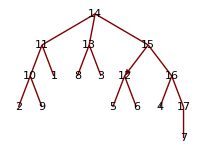
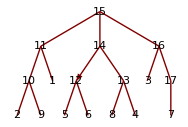
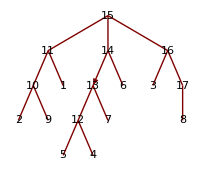
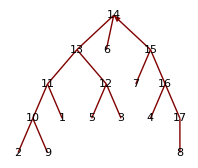
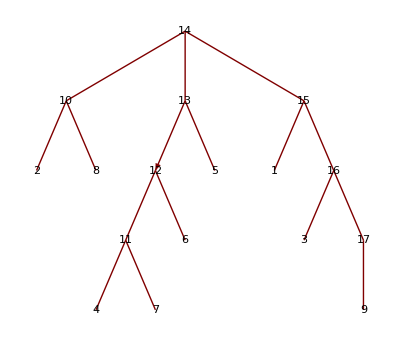
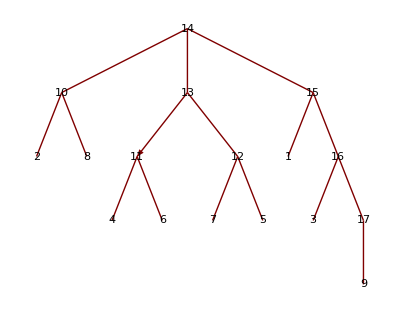
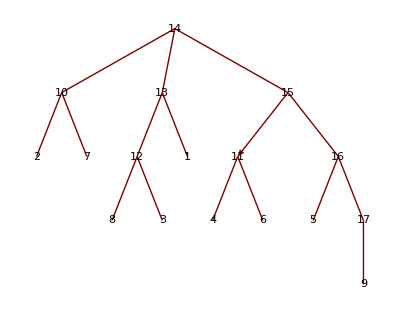
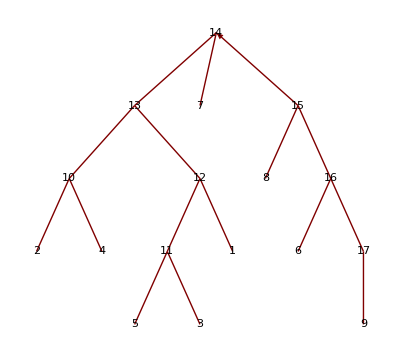
{{1,4,2,5},{3,8,4,9},{5,12,6,13},{9,17,10,16},{13,18,14,1},{17,14,18,15},{15,11,16,10},{11,6,12,7},{7,2,8,3}} | {{1,4,2,5},{3,8,4,9},{5,12,6,13},{9,17,10,16},{13,18,14,1},{17,14,18,15},{11,6,12,7},{15,11,16,10},{7,2,8,3}} | {{1,4,2,5},{3,8,4,9},{5,12,6,13},{9,17,10,16},{15,11,16,10},{13,18,14,1},{17,14,18,15},{11,6,12,7},{7,2,8,3}} | {{1,4,2,5},{3,8,4,9},{5,12,6,13},{9,17,10,16},{11,6,12,7},{13,18,14,1},{17,14,18,15},{15,11,16,10},{7,2,8,3}} | {{1,4,2,5},{5,12,6,13},{3,8,4,9},{9,17,10,16},{13,18,14,1},{17,14,18,15},{15,11,16,10},{11,6,12,7},{7,2,8,3}} | {{1,4,2,5},{5,12,6,13},{3,8,4,9},{13,18,14,1},{9,17,10,16},{17,14,18,15},{15,11,16,10},{11,6,12,7},{7,2,8,3}} | {{1,4,2,5},{5,12,6,13},{3,8,4,9},{13,18,14,1},{9,17,10,16},{17,14,18,15},{11,6,12,7},{7,2,8,3},{15,11,16,10}} | {{1,4,2,5},{5,12,6,13},{3,8,4,9},{11,6,12,7},{7,2,8,3},{9,17,10,16},{13,18,14,1},{17,14,18,15},{15,11,16,10}} | {{1,4,2,5},{9,17,10,16},{3,8,4,9},{5,12,6,13},{13,18,14,1},{17,14,18,15},{15,11,16,10},{11,6,12,7},{7,2,8,3}} | {{1,4,2,5},{9,17,10,16},{3,8,4,9},{13,18,14,1},{17,14,18,15},{15,11,16,10},{7,2,8,3},{5,12,6,13},{11,6,12,7}} | {{1,4,2,5},{13,18,14,1},{3,8,4,9},{9,17,10,16},{5,12,6,13},{17,14,18,15},{15,11,16,10},{11,6,12,7},{7,2,8,3}} | {{1,4,2,5},{13,18,14,1},{3,8,4,9},{9,17,10,16},{5,12,6,13},{17,14,18,15},{15,11,16,10},{7,2,8,3},{11,6,12,7}}
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[9,25]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

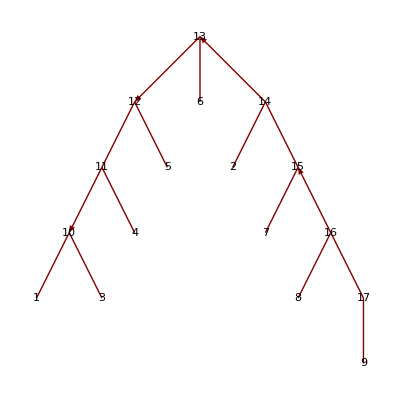
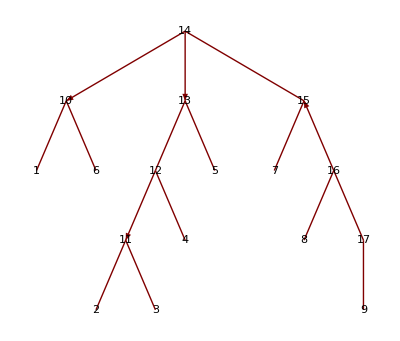
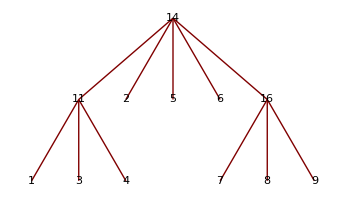
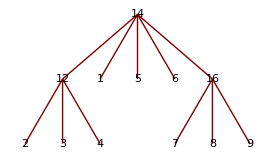
{{8,2,9,1},{12,4,13,3},{18,10,1,9},{10,18,11,17},{16,8,17,7},{2,12,3,11},{4,16,5,15},{14,6,15,5},{6,14,7,13}} | {{12,4,13,3},{8,2,9,1},{18,10,1,9},{10,18,11,17},{16,8,17,7},{2,12,3,11},{4,16,5,15},{14,6,15,5},{6,14,7,13}}
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[9,10]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

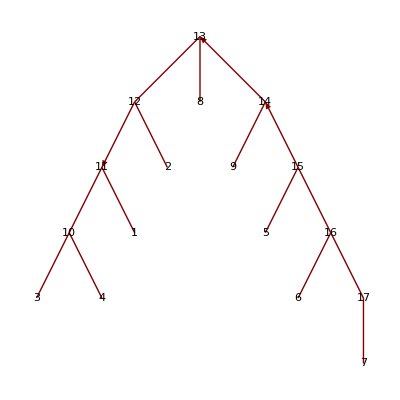
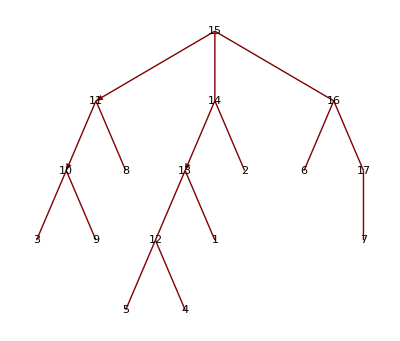
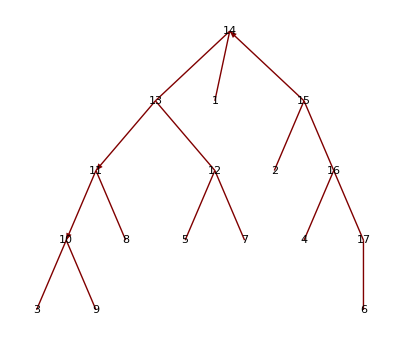
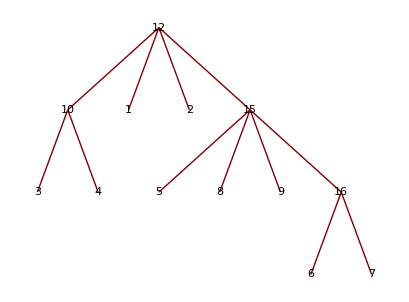
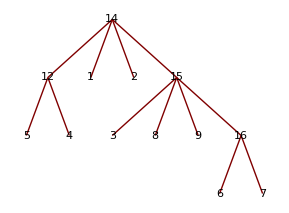
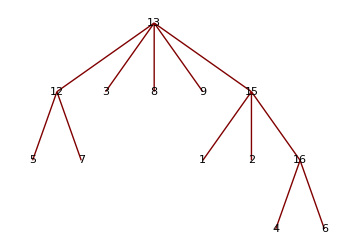
{{1,4,2,5},{7,10,8,11},{3,9,4,8},{9,3,10,2},{13,17,14,16},{5,15,6,14},{15,7,16,6},{11,1,12,18},{17,13,18,12}} | {{1,4,2,5},{7,10,8,11},{13,17,14,16},{3,9,4,8},{9,3,10,2},{5,15,6,14},{15,7,16,6},{11,1,12,18},{17,13,18,12}} | {{1,4,2,5},{7,10,8,11},{13,17,14,16},{3,9,4,8},{5,15,6,14},{9,3,10,2},{15,7,16,6},{11,1,12,18},{17,13,18,12}}
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[9,15]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

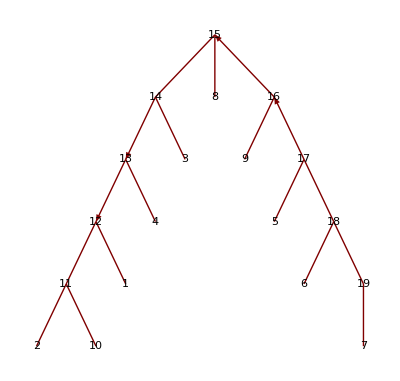
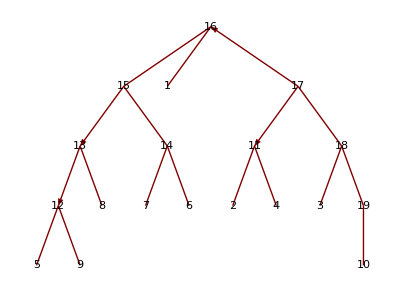
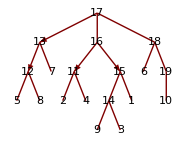
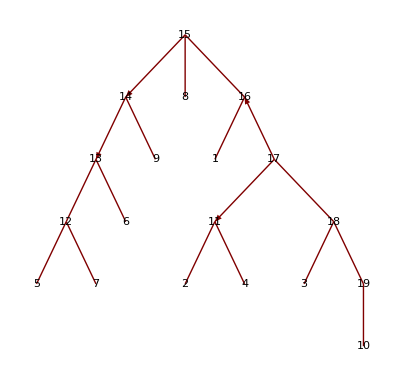
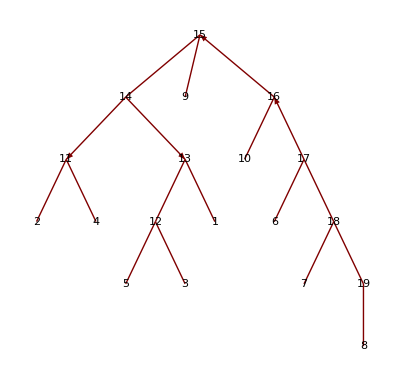
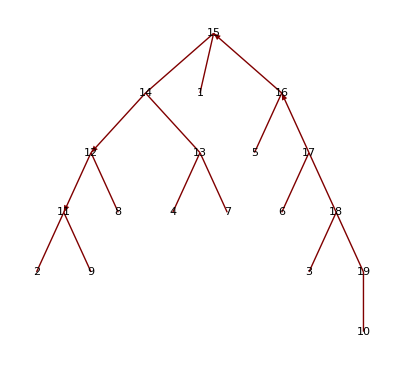
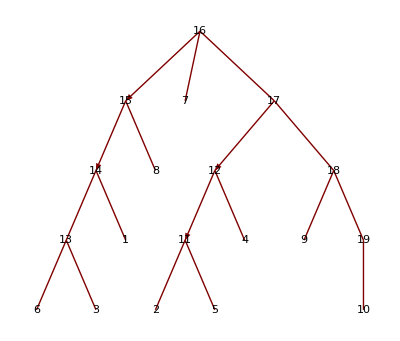
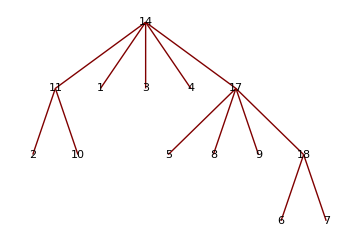
{{4,2,5,1},{10,4,11,3},{12,8,13,7},{8,12,9,11},{18,15,19,16},{16,5,17,6},{6,17,7,18},{20,13,1,14},{14,19,15,20},{2,10,3,9}} | {{4,2,5,1},{12,8,13,7},{10,4,11,3},{8,12,9,11},{18,15,19,16},{16,5,17,6},{6,17,7,18},{20,13,1,14},{14,19,15,20},{2,10,3,9}} | {{4,2,5,1},{12,8,13,7},{10,4,11,3},{8,12,9,11},{18,15,19,16},{16,5,17,6},{20,13,1,14},{14,19,15,20},{2,10,3,9},{6,17,7,18}} | {{4,2,5,1},{12,8,13,7},{10,4,11,3},{8,12,9,11},{16,5,17,6},{18,15,19,16},{6,17,7,18},{20,13,1,14},{14,19,15,20},{2,10,3,9}} | {{4,2,5,1},{12,8,13,7},{10,4,11,3},{8,12,9,11},{2,10,3,9},{18,15,19,16},{16,5,17,6},{6,17,7,18},{20,13,1,14},{14,19,15,20}} | {{4,2,5,1},{18,15,19,16},{10,4,11,3},{16,5,17,6},{12,8,13,7},{8,12,9,11},{6,17,7,18},{20,13,1,14},{14,19,15,20},{2,10,3,9}} | {{4,2,5,1},{18,15,19,16},{10,4,11,3},{20,13,1,14},{14,19,15,20},{2,10,3,9},{12,8,13,7},{8,12,9,11},{16,5,17,6},{6,17,7,18}}
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,37]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

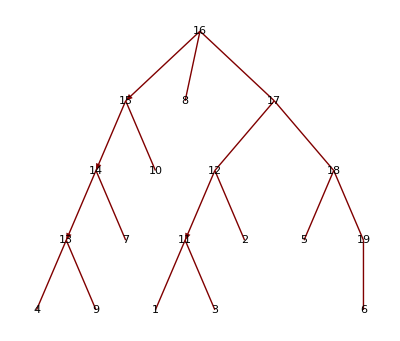
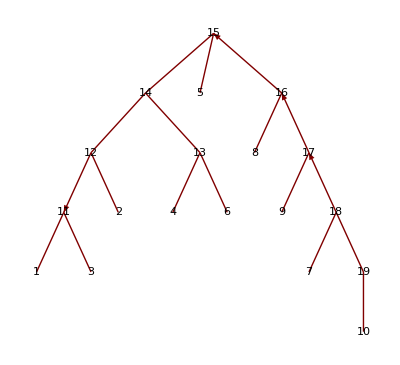
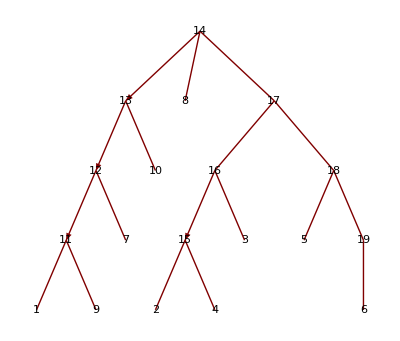
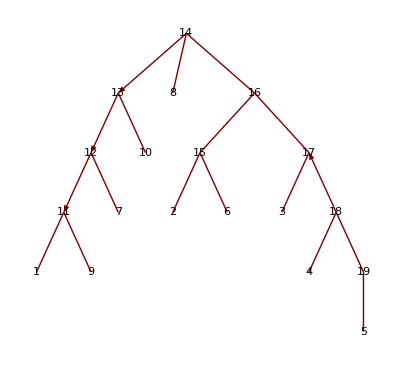
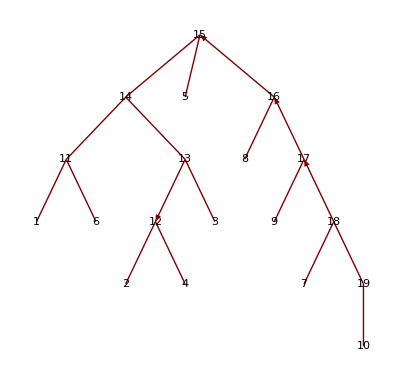
{{6,2,7,1},{8,4,9,3},{2,8,3,7},{16,10,17,9},{14,5,15,6},{4,15,5,16},{18,12,19,11},{20,14,1,13},{10,18,11,17},{12,20,13,19}} | {{6,2,7,1},{8,4,9,3},{2,8,3,7},{14,5,15,6},{16,10,17,9},{4,15,5,16},{18,12,19,11},{20,14,1,13},{10,18,11,17},{12,20,13,19}} | {{16,10,17,9},{6,2,7,1},{8,4,9,3},{2,8,3,7},{14,5,15,6},{4,15,5,16},{18,12,19,11},{20,14,1,13},{10,18,11,17},{12,20,13,19}} | {{16,10,17,9},{14,5,15,6},{6,2,7,1},{8,4,9,3},{2,8,3,7},{4,15,5,16},{18,12,19,11},{20,14,1,13},{10,18,11,17},{12,20,13,19}} | {{14,5,15,6},{6,2,7,1},{8,4,9,3},{2,8,3,7},{16,10,17,9},{4,15,5,16},{18,12,19,11},{20,14,1,13},{10,18,11,17},{12,20,13,19}} | {{14,5,15,6},{16,10,17,9},{6,2,7,1},{8,4,9,3},{2,8,3,7},{4,15,5,16},{18,12,19,11},{20,14,1,13},{10,18,11,17},{12,20,13,19}}
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,46]]]]]
```

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,128]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{{4,2,5,1},{8,4,9,3},{9,17,10,16},{5,15,6,14},{15,7,16,6},{13,1,14,20},{19,11,20,10},{11,19,12,18},{17,13,18,12},{2,8,3,7}} | {{4,2,5,1},{8,4,9,3},{9,17,10,16},{5,15,6,14},{13,1,14,20},{19,11,20,10},{15,7,16,6},{11,19,12,18},{17,13,18,12},{2,8,3,7}} | {{4,2,5,1},{9,17,10,16},{5,15,6,14},{8,4,9,3},{15,7,16,6},{13,1,14,20},{19,11,20,10},{11,19,12,18},{17,13,18,12},{2,8,3,7}} | {{4,2,5,1},{9,17,10,16},{5,15,6,14},{8,4,9,3},{15,7,16,6},{13,1,14,20},{2,8,3,7},{19,11,20,10},{11,19,12,18},{17,13,18,12}} | {{4,2,5,1},{9,17,10,16},{13,1,14,20},{19,11,20,10},{8,4,9,3},{5,15,6,14},{15,7,16,6},{11,19,12,18},{17,13,18,12},{2,8,3,7}} | {{4,2,5,1},{9,17,10,16},{13,1,14,20},{19,11,20,10},{8,4,9,3},{5,15,6,14},{11,19,12,18},{17,13,18,12},{2,8,3,7},{15,7,16,6}}
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
DrawPD[PD[Knot[10,128]]]
```

-Graphics-

```mathematica
DrawPD[PD[Knot[10,158]]]
```

-Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,158]]]]]
```

Part::partw: Part 8 of {{{6,2,7,1},{},1},{{11,18,12,19},{},6},{{20,16,1,15},{},9},{{19,12,20,13},{},10},{{{3,10,4,11},{9,2,10,3}},{{4,11},{2,9}},11},{{{8,14,9,13},{14,8,15,7}},{{9,13},{7,15}},12},{{{5,17,6,16},{17,5,18,4}},{{4,18},{6,16}},13}} does not exist.

Part::partw: Part 9 of {{{6,2,7,1},{},1},{{11,18,12,19},{},6},{{20,16,1,15},{},9},{{19,12,20,13},{},10},{{{3,10,4,11},{9,2,10,3}},{{4,11},{2,9}},11},{{{8,14,9,13},{14,8,15,7}},{{9,13},{7,15}},12},{{{5,17,6,16},{17,5,18,4}},{{4,18},{6,16}},13}} does not exist.

Part::partw: Part 10 of {{{6,2,7,1},{},1},{{11,18,12,19},{},6},{{20,16,1,15},{},9},{{19,12,20,13},{},10},{{{3,10,4,11},{9,2,10,3}},{{4,11},{2,9}},11},{{{8,14,9,13},{14,8,15,7}},{{9,13},{7,15}},12},{{{5,17,6,16},{17,5,18,4}},{{4,18},{6,16}},13}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{x,{},{}}

$Aborted

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[9,19]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{{1,4,2,5},{5,10,6,11},{3,9,4,8},{9,3,10,2},{13,16,14,17},{7,15,8,14},{15,7,16,6},{11,18,12,1},{17,12,18,13}} | {{1,4,2,5},{5,10,6,11},{13,16,14,17},{3,9,4,8},{9,3,10,2},{7,15,8,14},{15,7,16,6},{11,18,12,1},{17,12,18,13}} | {{1,4,2,5},{5,10,6,11},{13,16,14,17},{3,9,4,8},{7,15,8,14},{9,3,10,2},{15,7,16,6},{11,18,12,1},{17,12,18,13}}
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[9,21]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{13,1,14,18},{5,15,6,14},{17,7,18,6},{7,17,8,16},{15,9,16,8}}
-Graphics-
-Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[9,1]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{{1,10,2,11},{3,12,4,13},{5,14,6,15},{7,16,8,17},{9,18,10,1},{11,2,12,3},{13,4,14,5},{15,6,16,7},{17,8,18,9}}
-Graphics-
-Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[9,2]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

$Aborted

```mathematica
{{{{1,4,2,5},{3,12,4,13},{5,18,6,1},{7,16,8,17},{9,14,10,15},{13,10,14,11},{15,8,16,9},{17,6,18,7},{11,2,12,3}}}, {-Graphics-}, {TreePlot[removeEliminate[{10->1,10->3,{11->10,"eliminate"},11->8,{12->11,"eliminate"},12->4,{13->12,"eliminate"},13->7,{14->13,"eliminate"},14->5,{15->14,"eliminate"},15->6,16->15,16->2,17->16,17->9}],VertexLabeling->True]}}
```

{{1,4,2,5},{3,12,4,13},{5,18,6,1},{7,16,8,17},{9,14,10,15},{13,10,14,11},{15,8,16,9},{17,6,18,7},{11,2,12,3}}
-Graphics-
-Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,25]]]]]
```

{x,{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

TreePlot::grph: removeEliminate[{11→3,11→4,12→11,12→1,13→12,13→2,{14→13,eliminate},14→5,15→14,15→6,{16→15,eliminate},16→10,17→16,17→7,{18→17,eliminate},18→8,19→18,19→9}] is not a valid graph.

```mathematica
{{{{1,4,2,5},{5,14,6,15},{3,13,4,12},{13,3,14,2},{11,20,12,1},{19,6,20,7},{9,18,10,19},{7,16,8,17},{17,8,18,9},{15,10,16,11}}}, {-Graphics-}, {TreePlot[removeEliminate[{11->3,11->4,12->11,12->1,13->12,13->2,{14->13,"eliminate"},14->5,15->14,15->6,{16->15,"eliminate"},16->10,17->16,17->7,{18->17,"eliminate"},18->8,19->18,19->9}],VertexLabeling->True]}}
```

{{1,4,2,5},{5,14,6,15},{3,13,4,12},{13,3,14,2},{11,20,12,1},{19,6,20,7},{9,18,10,19},{7,16,8,17},{17,8,18,9},{15,10,16,11}}
-Graphics-
-Graphics-

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,59]]]]]
```

Part::partw: Part 7 of {{{14,8,15,7},{},5},{{18,12,19,11},{},6},{{12,18,13,17},{},9},{{6,14,7,13},{},10},{{{2,9,3,10},{8,3,9,4},{4,2,5,1},{10,6,11,5}},{{1,8},{6,11}},13},{{{16,19,17,20},{20,15,1,16}},{{17,19},{1,15}},14}} does not exist.

Part::partw: Part 8 of {{{14,8,15,7},{},5},{{18,12,19,11},{},6},{{12,18,13,17},{},9},{{6,14,7,13},{},10},{{{2,9,3,10},{8,3,9,4},{4,2,5,1},{10,6,11,5}},{{1,8},{6,11}},13},{{{16,19,17,20},{20,15,1,16}},{{17,19},{1,15}},14}} does not exist.

Part::partw: Part 9 of {{{14,8,15,7},{},5},{{18,12,19,11},{},6},{{12,18,13,17},{},9},{{6,14,7,13},{},10},{{{2,9,3,10},{8,3,9,4},{4,2,5,1},{10,6,11,5}},{{1,8},{6,11}},13},{{{16,19,17,20},{20,15,1,16}},{{17,19},{1,15}},14}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{x,{},{}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}},{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{x,{},{}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

{x,{x,{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{x,{},{}},{x,{},{}}}},{x,{x,{x,{x,{},{}},{x,{},{}}},{x,{},{}}},{x,{},{}}}},{x,{},{}}},{x,{},{}}}

```mathematica
Grid[overallTrees[removePDCode[PD[Knot[10,120]]]]]
```

### Check Cyclic Order

```mathematica
DrawPD[PD[Knot[8,6]]]
```

-Graphics-

```mathematica
knot86=removePDCode[PD[Knot[8,6]]]
```

{{1,4,2,5},{9,12,10,13},{3,11,4,10},{11,3,12,2},{5,14,6,15},{7,16,8,1},{15,6,16,7},{13,8,14,9}}

```mathematica
findTangle[knot86]
```

{{{1,4,2,5},{},1},{{3,11,4,10},{},3},{{11,3,12,2},{},4},{{5,14,6,15},{},5},{{7,16,8,1},{},6},{{15,6,16,7},{},7},{{{9,12,10,13},{13,8,14,9}},{{10,12},{8,14}},9}}

{{{1,4,2,5},{},1},{{5,14,6,15},{},5},{{7,16,8,1},{},6},{{15,6,16,7},{},7},{{{9,12,10,13},{13,8,14,9}},{{10,12},{8,14}},9},{{{3,11,4,10},{11,3,12,2}},{{4,10},{2,12}},10}}

{{{5,14,6,15},{},5},{{7,16,8,1},{},6},{{15,6,16,7},{},7},{{{9,12,10,13},{13,8,14,9}},{{10,12},{8,14}},9},{{{3,11,4,10},{11,3,12,2},{1,4,2,5}},{{10,12},{1,5}},11}}

{{{5,14,6,15},{},5},{{7,16,8,1},{},6},{{15,6,16,7},{},7},{{{9,12,10,13},{13,8,14,9},{3,11,4,10},{11,3,12,2},{1,4,2,5}},{{1,5},{8,14}},12}}

{{{7,16,8,1},{},6},{{15,6,16,7},{},7},{{{5,14,6,15},{9,12,10,13},{13,8,14,9},{3,11,4,10},{11,3,12,2},{1,4,2,5}},{{1,8},{6,15}},13}}

{{{15,6,16,7},{},7},{{{7,16,8,1},{5,14,6,15},{9,12,10,13},{13,8,14,9},{3,11,4,10},{11,3,12,2},{1,4,2,5}},{{6,15},{7,16}},14}}

{{{{15,6,16,7},{7,16,8,1},{5,14,6,15},{9,12,10,13},{13,8,14,9},{3,11,4,10},{11,3,12,2},{1,4,2,5}},{{},{}},15}}

{{9→2,9→8,10→3,10→4,11→10,11→1,{12→11,eliminate},{12→9,eliminate},13→12,13→5,{14→13,eliminate},14→6,15→14,15→7},-Graphics-}

```mathematica
TreePlot[removeEliminate[findTangle[knot86][[1]]],VertexLabeling->True]
```

-Graphics-

```mathematica
DrawPD[replacePDCode[{{1,11,2,10},{9,3,10,2},{3,14,4,15},{15,4,16,5},{5,16,6,1},{13,6,14,7},{7,12,8,13},{11,8,12,9}}]]
```

-Graphics-

```mathematica
TreePlot[removeEliminate[findTangle[{{1,11,2,10},{9,3,10,2},{3,14,4,15},{15,4,16,5},{5,16,6,1},{13,6,14,7},{7,12,8,13},{11,8,12,9}}][[1]]],VertexLabeling->True]
```

-Graphics-

### Get Flyping Circuits from Reduced Tree

```mathematica
flypeCircuits[knotPD_]:=Module[{output,nonReducedEdges,nonReducedTree,tangles,reducedEdges,descendantsMap,descendantsList,flypingCircuits,labeledCircuits,sortedTangles},
output=findTangle[knotPD];

nonReducedEdges=output[[1]];
nonReducedTree=output[[2]];
tangles=output[[3]];

reducedEdges=removeEliminate[nonReducedEdges];

descendantsMap=getChildrenAndParents[reducedEdges];
descendantsMap=Normal[descendantsMap];

(*check that each group of children is not entirely tangles and double-check that each group is not entirely singlecrossings*)
descendantsList=Table[descendantsMap[[i,2]],{i,1,Length[descendantsMap]}];

flypingCircuits=Table[
If[validCircuitCheck[descendantsList[[i]],tangles],
descendantsList[[i]],
Nothing
],
{i,1,Length[descendantsList]}
];

(*flypingCircuits=orderTangles[flypingCircuits];*)

sortedTangles=Sort[tangles,#1[[3]]<#2[[3]]&];

labeledCircuits=Table[
Table[
If[Length[sortedTangles[[flypingCircuits[[i,j]],2]]]==0,
(*then*){flypingCircuits[[i,j]],"c"},
(*else*){flypingCircuits[[i,j]],"t"}
]
,
{j,1,Length[flypingCircuits[[i]]]}
],
{i,1,Length[flypingCircuits]}
];

Return[{labeledCircuits,sortedTangles}];
]
```

```mathematica
orderTangles[flypingCircuits_]:=Module[{},

]
```

```mathematica
validCircuitCheck[possibleCircuit_,tangles_]:=Module[{tangleCount=0,singleCrossingCount=0,i,sortedTangles,tempIndex},
sortedTangles=Sort[tangles,#1[[3]]<#2[[3]]&];

For[i=1,i≤Length[possibleCircuit],i++,
tempIndex=possibleCircuit[[i]];
If[Length[sortedTangles[[tempIndex,2]]]==0,
(*then*)singleCrossingCount++,
(*else*)tangleCount++
];
];

If[singleCrossingCount>0&&tangleCount>0,
(*then*)Return[True],
(*else*)Return[False]
];
]
```

```mathematica
(*returns association*)
getChildrenAndParents[edgesLst_]:=Module[{edges=edgesLst,childMap,i,currentParent,parents,parentsparent},
childMap=makeChildMap[edges];
parents=Keys[childMap];

(*for each parent, get its parent and append it to the list of children*)
For[i=1,i≤Length[parents],i++,
currentParent=parents[[i]];

parentsparent=getParent[currentParent,edges];

If[parentsparent=="no parent",
Continue[]
];

AppendTo[childMap[currentParent],parentsparent];

];

Return[childMap];
]
```

```mathematica
getParent[index_,edges_]:=Module[{j},
For[j=1,j≤Length[edges],j++,
If[edges[[j,2]]==index,
(*then*)Return[edges[[j,1]]]
];
];

Return["no parent"];
]
```

#### Testing

```mathematica
TreePlot[removeEliminate[findTangle[removePDCode[PD[Knot[9,8]]]][[1]]],VertexLabeling->True]
```

-Graphics-

```mathematica
DrawPD@Knot[9,8]
```

-Graphics-

```mathematica
TreePlot[removeEliminate[findTangle[removePDCode[PD[Knot[9,23]]]][[1]]],VertexLabeling->True]
```

-Graphics-

```mathematica
DrawPD@Knot[9,29]
```

-Graphics-

```mathematica
TreePlot[removeEliminate[findTangle[removePDCode[PD[Knot[9,29]]]][[1]]],VertexLabeling->True]
```

-Graphics-

```mathematica
flypeCircuits[removePDCode[PD[Knot[8,15]]]]
```

{{{{2,c},{8,c},{10,t}},{{9,t},{1,c},{12,t}},{{3,c},{7,c},{12,t}},{{12,t},{4,c},{14,t}},{{5,c},{6,c},{13,t}}},{{{1,4,2,5},{},1},{{3,8,4,9},{},2},{{5,12,6,13},{},3},{{13,16,14,1},{},4},{{9,14,10,15},{},5},{{15,10,16,11},{},6},{{11,6,12,7},{},7},{{7,2,8,3},{},8},{{{3,8,4,9},{7,2,8,3}},{{4,9},{2,7}},9},{{{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{7,9},{1,5}},10},{{{5,12,6,13},{11,6,12,7}},{{5,13},{7,11}},11},{{{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{11,13},{1,9}},12},{{{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{9,11},{14,16}},13},{{{9,14,10,15},{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{11,16},{10,15}},14},{{{15,10,16,11},{9,14,10,15},{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{{},{}},15}}}

```mathematica
TreePlot[removeEliminate[findTangle[removePDCode[PD[Knot[8,15]]]][[1]]],VertexLabeling->True]
```

-Graphics-

```mathematica
flypeCircuits[removePDCode[PD[Knot[8,15]]]][[1]]
```

{{{2,c},{8,c},{10,t}},{{9,t},{1,c},{12,t}},{{3,c},{7,c},{12,t}},{{12,t},{4,c},{14,t}},{{5,c},{6,c},{13,t}}}

```mathematica
flypeCircuits[removePDCode[PD[Knot[9,18]]]][[1]]
```

{{{2,c},{9,c},{12,t}},{{1,c},{8,c},{10,t},{14,t}},{{3,c},{4,c},{12,t},{16,t}},{{5,c},{6,c},{7,c},{14,t}}}

```mathematica
TreePlot[removeEliminate[findTangle[removePDCode[PD[Knot[9,18]]]][[1]]],VertexLabeling->True]
```

-Graphics-

### Get Flypes from a Given Flyping Circuit

```mathematica
flypeCircuits[removePDCode[PD[Knot[8,15]]]][[1]]
```

{{{2,c},{8,c},{10,t}},{{9,t},{1,c},{12,t}},{{3,c},{7,c},{12,t}},{{12,t},{4,c},{14,t}},{{5,c},{6,c},{13,t}}}

```mathematica
getFlypes[circuitAndTangles_]:=Module[{circuits=circuitAndTangles[[1]],tangles=circuitAndTangles[[2]],i,j,tempCircuit,crossingsInCircuit,tanglesInCircuit,flypesInCircuit,PDflypes,possibleFlypes={}},
(*for each circuit*)
	(*for each crossing in the circuit, a flype can occur between that crossing and each tangle in its circuit*)
For[i=1,i≤Length[circuits],i++,
tempCircuit=circuits[[i]];
crossingsInCircuit=Select[tempCircuit,#[[2]]=="c"&];
tanglesInCircuit=Select[tempCircuit,#[[2]]=="t"&];
For[j=1,j≤Length[crossingsInCircuit],j++,
flypesInCircuit=Table[
{tanglesInCircuit[[k]],crossingsInCircuit[[j]]},
{k,1,Length[tanglesInCircuit]}
];
AppendTo[possibleFlypes,
flypesInCircuit
];
];
];

possibleFlypes=Flatten[possibleFlypes,1];

PDflypes=Table[
Table[
tangles[[possibleFlypes[[i,j,1]],1]]
,
{j,1,Length[possibleFlypes[[i]]]}
],
{i,1,Length[possibleFlypes]}
];

Return [{possibleFlypes,PDflypes}];
]
```

```mathematica
getFlypes[flypeCircuits[removePDCode[PD[Knot[8,15]]]]][[1]]
```

{{{10,t},{2,c}},{{10,t},{8,c}},{{9,t},{1,c}},{{12,t},{1,c}},{{12,t},{3,c}},{{12,t},{7,c}},{{12,t},{4,c}},{{14,t},{4,c}},{{13,t},{5,c}},{{13,t},{6,c}}}

```mathematica
Column[getFlypes[flypeCircuits[removePDCode[PD[Knot[8,15]]]]][[2]]]
```

{{{3,8,4,9},{7,2,8,3},{1,4,2,5}},{3,8,4,9}}
{{{3,8,4,9},{7,2,8,3},{1,4,2,5}},{7,2,8,3}}
{{{3,8,4,9},{7,2,8,3}},{1,4,2,5}}
{{{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{1,4,2,5}}
{{{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{5,12,6,13}}
{{{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{11,6,12,7}}
{{{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{13,16,14,1}}
{{{9,14,10,15},{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{13,16,14,1}}
{{{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{9,14,10,15}}
{{{13,16,14,1},{5,12,6,13},{11,6,12,7},{3,8,4,9},{7,2,8,3},{1,4,2,5}},{15,10,16,11}}

```mathematica
(*parFlype[knot,tangle,crossing]*)
```

```mathematica
drawpd[removePDCode[PD[Knot[8,15]]]]
```

-Graphics-

```mathematica
parFlype[removePDCode[PD[Knot[8,15]]],{{3,8,4,9},{7,2,8,3}},{1,4,2,5}]
```

Set::write: Tag Length in Length[{2,4}] is Protected.

{{1,6,2,7},{5,12,6,13},{7,2,8,3},{8,7,9,6},{9,14,10,15},{11,6,12,7},{13,16,14,1},{15,10,16,11}}

```mathematica
DrawPD[replacePDCode[{{1,6,2,7},{5,12,6,13},{7,2,8,3},{8,7,9,6},{9,14,10,15},{11,6,12,7},{13,16,14,1},{15,10,16,11}}]]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Mod::indet: Indeterminate expression Mod[0,0,1] encountered.

General::stop: Further output of Mod::indet will be suppressed during this calculation.

Part::pkspec1: The expression 23+{}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Compile::part: Part specification {}⟦1,1⟧ cannot be compiled since the argument is not a tensor of sufficient rank. Evaluation will use the uncompiled function.

Compile::cpintlt: Compile`$245 at position 2 of {KnotTheory`DrawPD`radius$7163,KnotTheory`DrawPD`radius$7164,KnotTheory`DrawPD`radius$7165,KnotTheory`DrawPD`radius$7166,KnotTheory`DrawPD`radius$7167,KnotTheory`DrawPD`radius$7168,KnotTheory`DrawPD`radius$7169,KnotTheory`DrawPD`radius$7170,KnotTheory`DrawPD`radius$7171,KnotTheory`DrawPD`radius$7172,«10»,KnotTheory`DrawPD`radius$7183,KnotTheory`DrawPD`radius$7184,KnotTheory`DrawPD`radius$7185,KnotTheory`DrawPD`radius$7186,KnotTheory`DrawPD`radius$7187,KnotTheory`DrawPD`radius$7188,KnotTheory`DrawPD`radius$7189,KnotTheory`DrawPD`radius$7190,KnotTheory`DrawPD`radius$7191,KnotTheory`DrawPD`radius$7192}⟦Compile`$245⟧ should be either a nonzero integer or a vector of nonzero integers; evaluation will use the uncompiled function.

CompiledFunction::cfex: Could not complete external evaluation at instruction 34; proceeding with uncompiled evaluation.

CompiledFunction::cfsa: Argument (1.61313 (1.+√(2.-2. Cos[0.125 Plus[«2»]])-1. Cos[0.125 (2.0944+6. ArcCos[«1»])]))/(1.+Cos[0.125 (2.0944+6. ArcCos[«1»])]) at position 2 should be a machine-size real number.

Transpose::nmtx: The first two levels of … cannot be transposed.

$Aborted

```mathematica
drawpd[{{1,6,2,7},{5,12,6,13},{7,2,8,3},{8,7,9,6},{9,14,10,15},{11,6,12,7},{13,16,14,1},{15,10,16,11}}]
```

Part::partw: Part 3 of Knot[MorseLink::Error: bad input] does not exist.

Part::partw: Part 2 of Knot[MorseLink::Error: bad input] does not exist.

Part::partw: Part 4 of Knot[MorseLink::Error: bad input] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
getFlypes[flypeCircuits[removePDCode[PD[Knot[9,18]]]]][[1]]
```

{{{12,t},{2,c}},{{12,t},{9,c}},{{10,t},{1,c}},{{14,t},{1,c}},{{10,t},{8,c}},{{14,t},{8,c}},{{12,t},{3,c}},{{16,t},{3,c}},{{12,t},{4,c}},{{16,t},{4,c}},{{14,t},{5,c}},{{14,t},{6,c}},{{14,t},{7,c}}}

```mathematica
Column[getFlypes[flypeCircuits[removePDCode[PD[Knot[9,18]]]]][[2]]]
```

{{{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{3,12,4,13}}
{{{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{11,2,12,3}}
{{{3,12,4,13},{11,2,12,3}},{1,4,2,5}}
{{{9,18,10,1},{5,14,6,15},{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{1,4,2,5}}
{{{3,12,4,13},{11,2,12,3}},{13,10,14,11}}
{{{9,18,10,1},{5,14,6,15},{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{13,10,14,11}}
{{{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{5,14,6,15}}
{{{7,16,8,17},{17,6,18,7},{9,18,10,1},{5,14,6,15},{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{5,14,6,15}}
{{{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{9,18,10,1}}
{{{7,16,8,17},{17,6,18,7},{9,18,10,1},{5,14,6,15},{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{9,18,10,1}}
{{{9,18,10,1},{5,14,6,15},{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{17,6,18,7}}
{{{9,18,10,1},{5,14,6,15},{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{7,16,8,17}}
{{{9,18,10,1},{5,14,6,15},{3,12,4,13},{11,2,12,3},{1,4,2,5},{13,10,14,11}},{15,8,16,9}}

```mathematica
drawpd[parFlype[removePDCode[PD[Knot[9,18]]],{{3,12,4,13},{11,2,12,3}},{13,10,14,11}]]
```

Set::write: Tag Length in Length[{11,13}] is Protected.

Part::partw: Part 3 of Knot[MorseLink::Error: bad input] does not exist.

Part::partw: Part 2 of Knot[MorseLink::Error: bad input] does not exist.

Part::partw: Part 4 of Knot[MorseLink::Error: bad input] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Hold[DrawMorseLink[MorseLink[MorseLink::Error: bad input],Gap→0.2]]

### Writhe Code

```mathematica
Writhe[PD_] := Module[{length,s2,s4,writhe,i,lowerLimit,pd},(*s2 stands for spot 2*)(*LL stands for lowerLimit*)
pd=PD;
length=Length[pd];
writhe = 0;
i=1;
lowerLimit=1;
While[i≤length,
s2=pd[[i,2]];
s4=pd[[i,4]];

(*true for the LL->2n, 2n->LL, LL->LL+1, LL+1->LL strands false for all others*)
If[s2==lowerLimit||s4==lowerLimit,
(*true for LL->2n or LL->LL+1 false for 2n->LL and LL+1->LL *)
If[s2==lowerLimit,
(*true for LL->LL+1 false for LL->2n *)
If[s4==(lowerLimit+1),writhe-=1,writhe+=1;lowerLimit=(pd[[i,4]])+1;],
(*true for LL+1->LL false for 2n->LL*)
If[s2==(lowerLimit+1),writhe+=1,writhe-=1;lowerLimit=(pd[[i,2]])+1]],

(*strands that are not LL->2n, 2n->LL, LL->LL+1, LL+1->LL*)
(*true for negative false for positive*)
If[s2<s4,writhe-=1,
writhe+=1]];
i++
];Return[writhe]]
```

```mathematica
Writhe[{{6,13,7,14},{14,7,15,8}}]
```

-2

### Main Function because I couldn’t find one if Trivan made one

```mathematica
(*Displays tree and indexed writhes*)
ShowTree[pd_]:=Module[{PD,tangleData,tangleList,writheAssoc=<||>,edgeList,removedEdgeList},
PD=removePDCode[pd];
tangleData=findTangle[PD];
tangleList=tangleData[[3]];
edgeList=tangleData[[1]];
removedEdgeList=removeEliminate[edgeList];
Print@removedEdgeList;
For[i=1,i≤Length@PD,i++,
AppendTo[writheAssoc,i->Writhe[{PD[[i]]}]]
];
Table[
If[KeyExistsQ[writheAssoc,link[[1]]],
writheAssoc[link[[1]]]+=writheAssoc[link[[2]]],
writheAssoc[link[[1]]]=writheAssoc[link[[2]]]
]
,{link,Sort@removedEdgeList}];
Print[writheAssoc];
Return[TreePlot[removedEdgeList,VertexLabeling->True,DirectedEdges->True]]
]
```

```mathematica
ShowTree[PD@Knot[9,13]]
```

{14→13,14→2,11→3,11→4,11→5,13→1,13→6,13→11,16→7,16→8,16→9,16→14}

<|1→1,2→1,3→1,4→1,5→1,6→1,7→1,8→1,9→1,11→3,13→5,14→6,16→9|>

-Graphics-

```mathematica
ExpandedWrithe[pd_]:=Module[{i,j,PD,tangleData,tangleList,writheAssoc=<||>,edgeList,removedEdgeList,childList={},newWritheAssoc=<||>,tempCounter,interiorEdgeList,tangleT},

PD=removePDCode[pd];
tangleData=findTangle[PD];
tangleList=tangleData[[3]];
edgeList=tangleData[[1]];
removedEdgeList=Sort@removeEliminate[edgeList];

For[i=1,i≤Length@PD,i++,
AppendTo[writheAssoc,i->Writhe[{PD[[i]]}]]
];

Table[

If[KeyExistsQ[writheAssoc,link[[1]]],
writheAssoc[link[[1]]]+=writheAssoc[link[[2]]],
writheAssoc[link[[1]]]=writheAssoc[link[[2]]]
]
,{link,removedEdgeList}];

For[i=Length@PD+1, i≤Max@Keys@writheAssoc,i++,
AppendTo[childList,Table[item[[2]],{item,Select[removedEdgeList,#[[1]]==i&]}]];
];

For[i=Length@PD+1,i≤Max@Keys@writheAssoc,i++,
tangleT=childList[[i-Length@PD]];

If[Length@tangleT==0,Continue[]];

tempCounter=0;
For[j=1,j≤Length@tangleT,j++,
If[tangleT[[j]]≤Length@PD,
tempCounter+=writheAssoc[tangleT[[j]]]
]
];

AppendTo[newWritheAssoc,i->tempCounter]
];

interiorEdgeList=Select[removedEdgeList,#[[2]]>Length@PD&];

(*Print@childList;*)
(*Print@newWritheAssoc;*)
(*Print@removedEdgeList;*)
(*Print@interiorEdgeList;*)


Return[{TreePlot[interiorEdgeList,VertexLabeling->True,DirectedEdges->True],newWritheAssoc,interiorEdgeList}]
]
```

```mathematica
ShowMoreEW[pdIn_]:=Module[{res={},pd=pdIn},
For[i=1,i≤9,i++,
AppendTo[res,ExpandedWrithe[pd]];
pd=RotateRight[pd];
];
Return[res]
]
```

```mathematica
FormattedEW[pd_]:=Module[{PD=pd,roughData,tree,writheAssoc,tangleAssoc,superTangles,subTangles,roots,result,rootStr="",i},
roughData=ExpandedWrithe[pd];
{tree,writheAssoc,tangleAssoc}=roughData;
superTangles=Keys[tangleAssoc];
subTangles=Values[tangleAssoc];
roots=Select[superTangles,!MemberQ[subTangles,#]&];
For[i=1,i≤Length@roots,i++,
If[i==1,
rootStr=rootStr<>recursiveSearch[tangleAssoc,roots[[i]],writheAssoc],
rootStr=rootStr<>","<>recursiveSearch[tangleAssoc,roots[[i]],writheAssoc]
];
];
result="["<>rootStr<>"]";
Return@result
]
```

```mathematica
recursiveSearch[tangleAssoc_,root_,writheAssoc_]:=Module[{subNodes,i,content},
subNodes=Values@Select[tangleAssoc,Keys[#]==root&];
If[Length@subNodes==0,Return[ToString@writheAssoc[root]<>""]];
content=ToString@writheAssoc[root]<>"[";
For[i=1,i≤Length@subNodes,i++,
If[i==1,
content=content<>recursiveSearch[tangleAssoc,subNodes[[i]],writheAssoc],
content=content<>","<>recursiveSearch[tangleAssoc,subNodes[[i]],writheAssoc]
];
];
content=content<>"]";
Return[content]
]
```

```mathematica
MoreFormattedEW[pd_]:=Module[{res={}},
For[i=1,i≤9,i++,
AppendTo[res,FormattedEW[pd]];
pd=RotateRight[pd];
];
Return[res]
]
```

```mathematica
MoreFormattedEW[PD@Knot[9,16]]
```

{[3[1[2,3]]],[3[1[2,3]]],[3[1[3,2]]],[3[1[3,2]]],[3[1[3,2]]],[2[1[3,3]]],[2[1[3,3]]],[2[1[3,3]]],[3[1[2,3]]]}